```mathematica
β[ω_,δ_,t_,ϵ_]:={{ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{-t,ⅈ δ-ϵ+ω,-t,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,-t,ⅈ δ-ϵ+ω,-t,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,-t,ⅈ δ-ϵ+ω,-t},{0,0,0,0,0,-t,ⅈ δ-ϵ+ω}}
```

```mathematica
T2[t_]:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}
```

```mathematica
T1[t_]:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}}
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,t,ϵ]],A:=Inverse[β[ω,δ,t,ϵ]],B:=Inverse[β[ω,δ,t,ϵ]],T1:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}},T2:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}},Do[J=Inverse[IdentityMatrix[7]-A.T1.Inverse[IdentityMatrix[7]-B.T2.J.T2].B.T1].A,4000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]
```

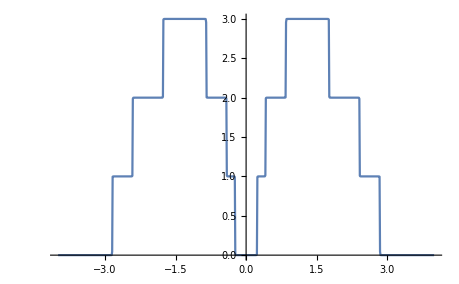

```mathematica
ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
ϕ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ϕ2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ϕ3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ϕ4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ϕ5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ϕ6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ϕ7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ϕ8[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ϕ9[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ϕ10[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ϕ11[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ϕ12[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ϕ13[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ϕ14[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
k514[ω_,ϵ1_]:=k514[ω,ϵ1]=Append[{},Table[ϕ14[ω,0.001,1,0,ϵ1],{i,500}]];
k513[ω_,ϵ1_]:=k513[ω,ϵ1]=Append[{},Table[ϕ13[ω,0.001,1,0,ϵ1],{i,500}]];
k512[ω_,ϵ1_]:=k512[ω,ϵ1]=Append[{},Table[ϕ12[ω,0.001,1,0,ϵ1],{i,500}]];
k511[ω_,ϵ1_]:=k511[ω,ϵ1]=Append[{},Table[ϕ11[ω,0.001,1,0,ϵ1],{i,500}]];
k510[ω_,ϵ1_]:=k510[ω,ϵ1]=Append[{},Table[ϕ10[ω,0.001,1,0,ϵ1],{i,500}]];
k59[ω_,ϵ1_]:=k59[ω,ϵ1]=Append[{},Table[ϕ9[ω,0.001,1,0,ϵ1],{i,500}]];
k58[ω_,ϵ1_]:=k58[ω,ϵ1]=Append[{},Table[ϕ8[ω,0.001,1,0,ϵ1],{i,500}]];
k57[ω_,ϵ1_]:=k57[ω,ϵ1]=Append[{},Table[ϕ7[ω,0.001,1,0,ϵ1],{i,500}]];
k56[ω_,ϵ1_]:=k56[ω,ϵ1]=Append[{},Table[ϕ6[ω,0.001,1,0,ϵ1],{i,500}]];
k55[ω_,ϵ1_]:=k55[ω,ϵ1]=Append[{},Table[ϕ5[ω,0.001,1,0,ϵ1],{i,500}]];
k54[ω_,ϵ1_]:=k54[ω,ϵ1]=Append[{},Table[ϕ4[ω,0.001,1,0,ϵ1],{i,500}]];
k53[ω_,ϵ1_]:=k53[ω,ϵ1]=Append[{},Table[ϕ3[ω,0.001,1,0,ϵ1],{i,500}]];
k52[ω_,ϵ1_]:=k52[ω,ϵ1]=Append[{},Table[ϕ2[ω,0.001,1,0,ϵ1],{i,500}]];
k51[ω_,ϵ1_]:=k51[ω,ϵ1]=Append[{},Table[ϕ1[ω,0.001,1,0,ϵ1],{i,500}]]
```

```mathematica
ρ5[ω_,ϵ1_]:=Join[Mean[k51[ω,ϵ1]],Mean[k52[ω,ϵ1]],Mean[k53[ω,ϵ1]],Mean[k54[ω,ϵ1]],Mean[k55[ω,ϵ1]],Mean[k56[ω,ϵ1]],Mean[k57[ω,ϵ1]],Mean[k58[ω,ϵ1]],Mean[k59[ω,ϵ1]],Mean[k510[ω,ϵ1]],Mean[k511[ω,ϵ1]],Mean[k513[ω,ϵ1]],Mean[k514[ω,ϵ1]]]
```

```mathematica
Mean[ρ5[0.5,0.5]]
```

1.68049

```mathematica
ListLinePlot[Table[{ω,Mean[ρ5[ω,0.5]]},{ω,Range[0,4,0.05]}]]
```

$Aborted

## 4 IMPURITIES

```mathematica
θ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
θ2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
θ3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
θ4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
θ5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
θ6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
θ7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
θ8[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
θ9[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
θ10[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
θ11[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
θ12[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
θ13[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
θ14[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
k414[ω_,ϵ1_]:=k414[ω,ϵ1]=Append[{},Table[θ14[ω,0.001,1,0,ϵ1],{i,500}]];
k413[ω_,ϵ1_]:=k413[ω,ϵ1]=Append[{},Table[θ13[ω,0.001,1,0,ϵ1],{i,500}]];
k412[ω_,ϵ1_]:=k412[ω,ϵ1]=Append[{},Table[θ12[ω,0.001,1,0,ϵ1],{i,500}]];
k411[ω_,ϵ1_]:=k411[ω,ϵ1]=Append[{},Table[θ11[ω,0.001,1,0,ϵ1],{i,500}]];
k410[ω_,ϵ1_]:=k410[ω,ϵ1]=Append[{},Table[θ10[ω,0.001,1,0,ϵ1],{i,500}]];
k49[ω_,ϵ1_]:=k49[ω,ϵ1]=Append[{},Table[θ9[ω,0.001,1,0,ϵ1],{i,500}]];
k48[ω_,ϵ1_]:=k48[ω,ϵ1]=Append[{},Table[θ8[ω,0.001,1,0,ϵ1],{i,500}]];
k47[ω_,ϵ1_]:=k47[ω,ϵ1]=Append[{},Table[θ7[ω,0.001,1,0,ϵ1],{i,500}]];
k46[ω_,ϵ1_]:=k46[ω,ϵ1]=Append[{},Table[θ6[ω,0.001,1,0,ϵ1],{i,500}]];
k45[ω_,ϵ1_]:=k45[ω,ϵ1]=Append[{},Table[θ5[ω,0.001,1,0,ϵ1],{i,500}]];
k44[ω_,ϵ1_]:=k44[ω,ϵ1]=Append[{},Table[θ4[ω,0.001,1,0,ϵ1],{i,500}]];
k43[ω_,ϵ1_]:=k43[ω,ϵ1]=Append[{},Table[θ3[ω,0.001,1,0,ϵ1],{i,500}]];
k42[ω_,ϵ1_]:=k42[ω,ϵ1]=Append[{},Table[θ2[ω,0.001,1,0,ϵ1],{i,500}]];
k41[ω_,ϵ1_]:=k41[ω,ϵ1]=Append[{},Table[θ1[ω,0.001,1,0,ϵ1],{i,500}]]
```

```mathematica
ρ4[ω_,ϵ1_]:=Join[Mean[k41[ω,ϵ1]],Mean[k42[ω,ϵ1]],Mean[k43[ω,ϵ1]],Mean[k44[ω,ϵ1]],Mean[k45[ω,ϵ1]],Mean[k46[ω,ϵ1]],Mean[k47[ω,ϵ1]],Mean[k48[ω,ϵ1]],Mean[k49[ω,ϵ1]],Mean[k410[ω,ϵ1]],Mean[k411[ω,ϵ1]],Mean[k413[ω,ϵ1]],Mean[k414[ω,ϵ1]]]
```

```mathematica
Mean[ρ4[0.5,0.5]]
```

1.76279

```mathematica
StandardDeviation[ρ4[0.5,0.5]]
```

0.127738

```mathematica
σ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
σ2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
σ3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
σ4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
σ5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
σ6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
σ7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
σ8[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
σ9[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
σ10[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
σ11[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
σ12[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
σ13[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
σ14[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
k314[ω_,ϵ1_]:=k314[ω,ϵ1]=Append[{},Table[σ14[ω,0.001,1,0,ϵ1],{i,500}]];
k313[ω_,ϵ1_]:=k313[ω,ϵ1]=Append[{},Table[σ13[ω,0.001,1,0,ϵ1],{i,500}]];
k312[ω_,ϵ1_]:=k312[ω,ϵ1]=Append[{},Table[σ12[ω,0.001,1,0,ϵ1],{i,500}]];
k311[ω_,ϵ1_]:=k311[ω,ϵ1]=Append[{},Table[σ11[ω,0.001,1,0,ϵ1],{i,500}]];
k310[ω_,ϵ1_]:=k310[ω,ϵ1]=Append[{},Table[σ10[ω,0.001,1,0,ϵ1],{i,500}]];
k39[ω_,ϵ1_]:=k39[ω,ϵ1]=Append[{},Table[σ9[ω,0.001,1,0,ϵ1],{i,500}]];
k38[ω_,ϵ1_]:=k38[ω,ϵ1]=Append[{},Table[σ8[ω,0.001,1,0,ϵ1],{i,500}]];
k37[ω_,ϵ1_]:=k37[ω,ϵ1]=Append[{},Table[σ7[ω,0.001,1,0,ϵ1],{i,500}]];
k36[ω_,ϵ1_]:=k36[ω,ϵ1]=Append[{},Table[σ6[ω,0.001,1,0,ϵ1],{i,500}]];
k35[ω_,ϵ1_]:=k35[ω,ϵ1]=Append[{},Table[σ5[ω,0.001,1,0,ϵ1],{i,500}]];
k34[ω_,ϵ1_]:=k34[ω,ϵ1]=Append[{},Table[σ4[ω,0.001,1,0,ϵ1],{i,500}]];
k33[ω_,ϵ1_]:=k33[ω,ϵ1]=Append[{},Table[σ3[ω,0.001,1,0,ϵ1],{i,500}]];
k32[ω_,ϵ1_]:=k32[ω,ϵ1]=Append[{},Table[σ2[ω,0.001,1,0,ϵ1],{i,500}]];
k31[ω_,ϵ1_]:=k31[ω,ϵ1]=Append[{},Table[σ1[ω,0.001,1,0,ϵ1],{i,500}]]
```

```mathematica
ρ3[ω_,ϵ1_]:=Join[Mean[k31[ω,ϵ1]],Mean[k32[ω,ϵ1]],Mean[k33[ω,ϵ1]],Mean[k34[ω,ϵ1]],Mean[k35[ω,ϵ1]],Mean[k36[ω,ϵ1]],Mean[k37[ω,ϵ1]],Mean[k38[ω,ϵ1]],Mean[k39[ω,ϵ1]],Mean[k310[ω,ϵ1]],Mean[k311[ω,ϵ1]],Mean[k313[ω,ϵ1]],Mean[k314[ω,ϵ1]]]
```

```mathematica
Mean[ρ3[0.5,0.5]]
```

1.82906

```mathematica
μ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
μ2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
μ3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
μ4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
μ5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
μ6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
μ7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
k27[ω_,ϵ1_]:=k27[ω,ϵ1]=Append[{},Table[μ7[ω,0.001,1,0,ϵ1],{i,500}]];
k26[ω_,ϵ1_]:=k26[ω,ϵ1]=Append[{},Table[μ6[ω,0.001,1,0,ϵ1],{i,500}]];
k25[ω_,ϵ1_]:=k25[ω,ϵ1]=Append[{},Table[μ5[ω,0.001,1,0,ϵ1],{i,500}]];
k24[ω_,ϵ1_]:=k24[ω,ϵ1]=Append[{},Table[μ4[ω,0.001,1,0,ϵ1],{i,500}]];
k23[ω_,ϵ1_]:=k23[ω,ϵ1]=Append[{},Table[μ3[ω,0.001,1,0,ϵ1],{i,500}]];
k22[ω_,ϵ1_]:=k22[ω,ϵ1]=Append[{},Table[μ2[ω,0.001,1,0,ϵ1],{i,500}]];
k21[ω_,ϵ1_]:=k21[ω,ϵ1]=Append[{},Table[μ1[ω,0.001,1,0,ϵ1],{i,500}]]
```

```mathematica
ρ2[ω_,ϵ1_]:=Join[Mean[k21[ω,ϵ1]],Mean[k22[ω,ϵ1]],Mean[k23[ω,ϵ1]],Mean[k24[ω,ϵ1]],Mean[k25[ω,ϵ1]],Mean[k26[ω,ϵ1]],Mean[k27[ω,ϵ1]]]
```

```mathematica
Mean[ρ2[0.5,0.5]]
```

1.89602

```mathematica
StandardDeviation[ρ2[0.5,0.5]]
```

0.0617823

```mathematica
β1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
β2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
β3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
β4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
β5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
β6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
β7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
β8[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
β9[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
β10[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
β11[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
β12[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
β13[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
β14[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
k614[ω_,ϵ1_]:=k614[ω,ϵ1]=Append[{},Table[β14[ω,0.001,1,0,ϵ1],{i,500}]];
k613[ω_,ϵ1_]:=k613[ω,ϵ1]=Append[{},Table[β13[ω,0.001,1,0,ϵ1],{i,500}]];
k612[ω_,ϵ1_]:=k612[ω,ϵ1]=Append[{},Table[β12[ω,0.001,1,0,ϵ1],{i,500}]];
k611[ω_,ϵ1_]:=k611[ω,ϵ1]=Append[{},Table[β11[ω,0.001,1,0,ϵ1],{i,500}]];
k610[ω_,ϵ1_]:=k610[ω,ϵ1]=Append[{},Table[β10[ω,0.001,1,0,ϵ1],{i,500}]];
k69[ω_,ϵ1_]:=k69[ω,ϵ1]=Append[{},Table[β9[ω,0.001,1,0,ϵ1],{i,500}]];
k68[ω_,ϵ1_]:=k68[ω,ϵ1]=Append[{},Table[β8[ω,0.001,1,0,ϵ1],{i,500}]];
k67[ω_,ϵ1_]:=k67[ω,ϵ1]=Append[{},Table[β7[ω,0.001,1,0,ϵ1],{i,500}]];
k66[ω_,ϵ1_]:=k66[ω,ϵ1]=Append[{},Table[β6[ω,0.001,1,0,ϵ1],{i,500}]];
k65[ω_,ϵ1_]:=k65[ω,ϵ1]=Append[{},Table[β5[ω,0.001,1,0,ϵ1],{i,500}]];
k64[ω_,ϵ1_]:=k64[ω,ϵ1]=Append[{},Table[β4[ω,0.001,1,0,ϵ1],{i,500}]];
k63[ω_,ϵ1_]:=k63[ω,ϵ1]=Append[{},Table[β3[ω,0.001,1,0,ϵ1],{i,500}]];
k62[ω_,ϵ1_]:=k62[ω,ϵ1]=Append[{},Table[β2[ω,0.001,1,0,ϵ1],{i,500}]];
k61[ω_,ϵ1_]:=k61[ω,ϵ1]=Append[{},Table[β1[ω,0.001,1,0,ϵ1],{i,500}]]
```

```mathematica
ρ6[ω_,ϵ1_]:=Join[Mean[k61[ω,ϵ1]],Mean[k62[ω,ϵ1]],Mean[k63[ω,ϵ1]],Mean[k64[ω,ϵ1]],Mean[k65[ω,ϵ1]],Mean[k66[ω,ϵ1]],Mean[k67[ω,ϵ1]],Mean[k68[ω,ϵ1]],Mean[k69[ω,ϵ1]],Mean[k610[ω,ϵ1]],Mean[k611[ω,ϵ1]],Mean[k613[ω,ϵ1]],Mean[k614[ω,ϵ1]]]
```

```mathematica
Lmean[ω_,ϵ1_]:={{4,Mean[ρ2[ω,ϵ1]]},{6,Mean[ρ3[ω,ϵ1]]},{8,Mean[ρ4[ω,ϵ1]]},{10,Mean[ρ5[ω,ϵ1]]},{12,Mean[ρ6[ω,ϵ1]]},{14,Mean[ρ7[ω,ϵ1]]},{16,Mean[ρ8[ω,ϵ1]]}}
```

```mathematica
Lstdmin[ω_,ϵ1_]:={{4,Mean[ρ2[ω,ϵ1]]-StandardDeviation[ρ2[ω,ϵ1]]},{6,Mean[ρ3[ω,ϵ1]]-StandardDeviation[ρ3[ω,ϵ1]]},{8,Mean[ρ4[ω,ϵ1]]-StandardDeviation[ρ4[ω,ϵ1]]},{10,Mean[ρ5[ω,ϵ1]]-StandardDeviation[ρ5[ω,ϵ1]]},{12,Mean[ρ6[ω,ϵ1]]-StandardDeviation[ρ6[ω,ϵ1]]},{14,Mean[ρ7[ω,ϵ1]]-StandardDeviation[ρ7[ω,ϵ1]]},{16,Mean[ρ8[ω,ϵ1]]-StandardDeviation[ρ8[ω,ϵ1]]}}
```

```mathematica
Lstdmax[ω_,ϵ1_]:={{4,Mean[ρ2[ω,ϵ1]]+StandardDeviation[ρ2[ω,ϵ1]]},{6,Mean[ρ3[ω,ϵ1]]+StandardDeviation[ρ3[ω,ϵ1]]},{8,Mean[ρ4[ω,ϵ1]]+StandardDeviation[ρ4[ω,ϵ1]]},{10,Mean[ρ5[ω,ϵ1]]+StandardDeviation[ρ5[ω,ϵ1]]},{12,Mean[ρ6[ω,ϵ1]]+StandardDeviation[ρ6[ω,ϵ1]]},{14,Mean[ρ7[ω,ϵ1]]+StandardDeviation[ρ7[ω,ϵ1]]},{16,Mean[ρ8[ω,ϵ1]]+StandardDeviation[ρ8[ω,ϵ1]]}}
```

```mathematica
λ[ω_,ϵ1_]:=Show[ListLinePlot[Lmean[ω,ϵ1],PlotRange->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm[T],None},{HoldForm[μ],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}],ListLinePlot[Lstdmin[ω,ϵ1],FrameLabel->{{HoldForm[T],None},{HoldForm[μ],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]},PlotRange->All,PlotStyle->Red,PlotStyle->Dashed,PlotTheme->"Detailed"],ListLinePlot[Lstdmax[ω,ϵ1],PlotRange->All,PlotStyle->Green,PlotTheme->"Detailed",FrameLabel->{{HoldForm[T],None},{HoldForm[μ],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}],PlotRange->All]
```

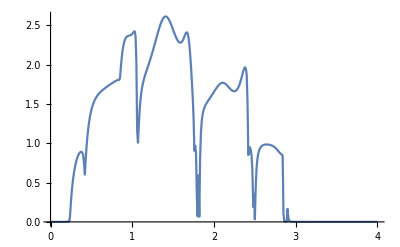

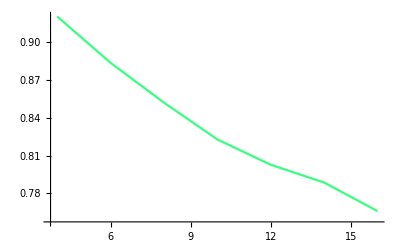

```mathematica
ListLinePlot[Lmean[.4,0.5],PlotStyle->RGBColor[RandomReal[{0,0.25}],1,RandomReal[{0.5,0.7}]]]
```

```mathematica
ListLinePlot[Lmean[0.3,0.5],PlotStyle->Red]
```

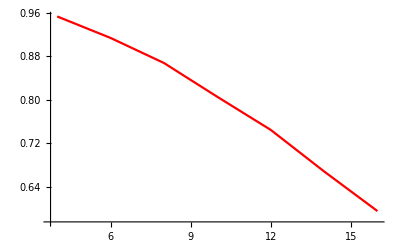

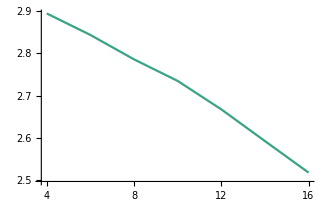

```mathematica
ListLinePlot[Lmean[1,0.5],PlotStyle->RGBColor[RandomReal[{0,0.5}],0.64,RandomReal[{0.5,0.8}]]]
```

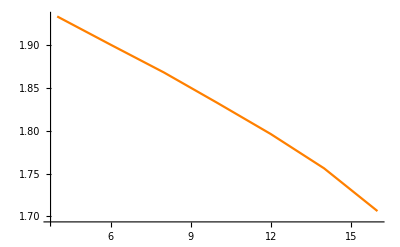

```mathematica
ListLinePlot[Lmean[0.6,0.5],PlotStyle->Orange]
```

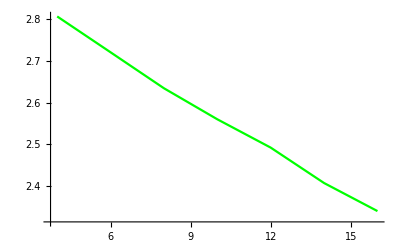

```mathematica
ListLinePlot[Lmean[1.3,0.5],PlotStyle->Green,PlotTheme->"Detailed"]
```

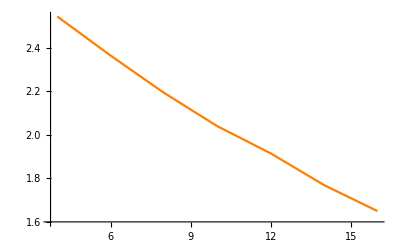

```mathematica
ListLinePlot[Lmean[1.1,0.5],PlotStyle->Orange,PlotTheme->"Detailed"]
```

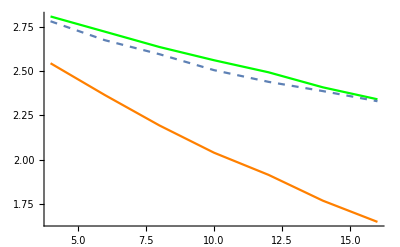

```mathematica
Show[%965,%964,%966,PlotRange->All]
```

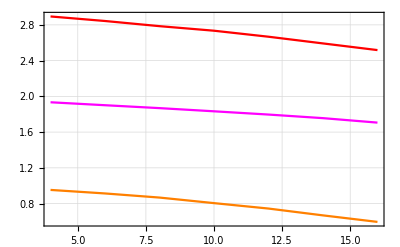

```mathematica
Show[ListLinePlot[Lmean[0.3,0.5],PlotStyle->Orange,PlotTheme->"Detailed"],ListLinePlot[Lmean[01,0.5],PlotStyle->Red,PlotTheme->"Detailed"],ListLinePlot[Lmean[0.6,0.5],PlotStyle->RGBColor[1,0,1],PlotTheme->"Detailed"],PlotRange->All]
```

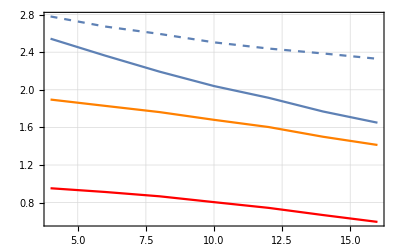

```mathematica
{{0.5,1.424989975144958},{1.5,2.4429313736944893},{0.3,0.7037773050485623}}
```

```mathematica
A={{0.3,0.8489331083188443},{0.6,1.8329244025920222},{1.,2.6692479988331064}}
```

{{0.3,0.848933},{0.6,1.83292},{1.,2.66925}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m1=Table[{ω,If[ψψ[ω,0.001,1,0,0.5]>3,3,ψψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000281572},{0.01,0.0000232127},{0.02,7.8554×10^-6},{0.03,0.0000178497},{0.04,0.0000541802},{0.05,0.000101769},{0.06,0.000161639},{0.07,0.00023527},{0.08,0.000324694},{0.09,0.000432642},{0.1,0.000562768},{0.11,0.000719961},{0.12,0.000910837},{0.13,0.00114448},{0.14,0.00143363},{0.15,0.00179661},{0.16,0.00226074},{0.17,0.00286844},{0.18,0.0036894},{0.19,0.00484667},{0.2,0.00658088},{0.21,0.00943956},{0.22,0.0150306},{0.23,0.0314864},{0.24,0.389069},{0.25,0.671888},{0.26,0.771869},{0.27,0.822629},{0.28,0.853409},{0.29,0.874153},{0.3,0.889139},{0.31,0.900494},{0.32,0.909379},{0.33,0.91647},{0.34,0.922161},{0.35,0.926671},{0.36,0.930079},{0.37,0.932312},{0.38,0.933046},{0.39,0.931371},{0.4,0.92434},{0.41,0.895228},{0.42,1.14429},{0.43,1.4936},{0.44,1.67419},{0.45,1.77536},{0.46,1.83461},{0.47,1.86985},{0.48,1.89055},{0.49,1.90215},{0.5,1.9079},{0.51,1.90986},{0.52,1.90937},{0.53,1.90731},{0.54,1.90428},{0.55,1.90071},{0.56,1.89689},{0.57,1.89302},{0.58,1.88925},{0.59,1.88569},{0.6,1.8824},{0.61,1.87944},{0.62,1.87684},{0.63,1.87462},{0.64,1.87278},{0.65,1.87134},{0.66,1.87027},{0.67,1.86957},{0.68,1.86919},{0.69,1.86912},{0.7,1.86929},{0.71,1.86965},{0.72,1.87013},{0.73,1.87063},{0.74,1.87102},{0.75,1.87115},{0.76,1.8708},{0.77,1.86968},{0.78,1.86733},{0.79,1.86308},{0.8,1.85572},{0.81,1.84304},{0.82,1.82013},{0.83,1.77336},{0.84,1.64286},{0.85,1.08874},{0.86,1.93574},{0.87,2.30675},{0.88,2.49658},{0.89,2.60721},{0.9,2.678},{0.91,2.72691},{0.92,2.76304},{0.93,2.79135},{0.94,2.81465},{0.95,2.83455},{0.96,2.85192},{0.97,2.86711},{0.98,2.87995},{0.99,2.88961},{1.,2.89404},{1.01,2.88865},{1.02,2.86266},{1.03,2.78891},{1.04,2.59389},{1.05,2.08579},{1.06,1.19185},{1.07,1.21911},{1.08,1.71685},{1.09,2.05742},{1.1,2.26039},{1.11,2.38462},{1.12,2.46449},{1.13,2.51817},{1.14,2.55559},{1.15,2.58247},{1.16,2.60227},{1.17,2.61723},{1.18,2.62884},{1.19,2.63815},{1.2,2.64589},{1.21,2.65261},{1.22,2.65871},{1.23,2.66449},{1.24,2.67018},{1.25,2.67593},{1.26,2.68186},{1.27,2.68803},{1.28,2.69447},{1.29,2.70118},{1.3,2.70812},{1.31,2.71523},{1.32,2.72241},{1.33,2.72954},{1.34,2.73647},{1.35,2.74301},{1.36,2.74897},{1.37,2.75411},{1.38,2.75822},{1.39,2.76104},{1.4,2.76234},{1.41,2.7619},{1.42,2.75953},{1.43,2.75511},{1.44,2.74856},{1.45,2.73989},{1.46,2.72921},{1.47,2.71668},{1.48,2.70261},{1.49,2.68735},{1.5,2.67135},{1.51,2.65508},{1.52,2.63907},{1.53,2.62387},{1.54,2.61002},{1.55,2.59804},{1.56,2.58846},{1.57,2.58174},{1.58,2.57832},{1.59,2.57854},{1.6,2.58265},{1.61,2.59067},{1.62,2.60225},{1.63,2.61646},{1.64,2.6314},{1.65,2.64382},{1.66,2.64882},{1.67,2.64003},{1.68,2.61077},{1.69,2.55621},{1.7,2.47557},{1.71,2.37253},{1.72,2.25288},{1.73,2.12027},{1.74,1.97121},{1.75,1.78637},{1.76,1.49565},{1.77,1.1003},{1.78,0.0106008},{1.79,3},{1.8,3},{1.81,1.26762},{1.82,0.565509},{1.83,1.14978},{1.84,1.40018},{1.85,1.5299},{1.86,1.60652},{1.87,1.65662},{1.88,1.69232},{1.89,1.71975},{1.9,1.74227},{1.91,1.76182},{1.92,1.77954},{1.93,1.79609},{1.94,1.81186},{1.95,1.82699},{1.96,1.8415},{1.97,1.85529},{1.98,1.86817},{1.99,1.87987},{2.,1.89011},{2.01,1.89856},{2.02,1.9049},{2.03,1.90884},{2.04,1.91016},{2.05,1.9087},{2.06,1.90442},{2.07,1.89736},{2.08,1.88772},{2.09,1.87576},{2.1,1.86186},{2.11,1.84646},{2.12,1.83005},{2.13,1.81315},{2.14,1.79625},{2.15,1.77984},{2.16,1.76436},{2.17,1.75021},{2.18,1.73771},{2.19,1.72714},{2.2,1.71867},{2.21,1.7124},{2.22,1.70831},{2.23,1.70621},{2.24,1.70574},{2.25,1.70627},{2.26,1.70689},{2.27,1.70634},{2.28,1.7031},{2.29,1.69545},{2.3,1.68181},{2.31,1.66106},{2.32,1.63289},{2.33,1.59804},{2.34,1.55813},{2.35,1.51536},{2.36,1.47193},{2.37,1.42953},{2.38,1.3888},{2.39,1.34826},{2.4,1.29894},{2.41,1.14879},{2.42,0.187211},{2.43,0.460481},{2.44,3},{2.45,3},{2.46,0.386849},{2.47,0.386169},{2.48,0.627733},{2.49,0.732756},{2.5,0.788234},{2.51,0.821806},{2.52,0.844491},{2.53,0.861417},{2.54,0.875248},{2.55,0.887482},{2.56,0.899002},{2.57,0.910321},{2.58,0.92171},{2.59,0.933249},{2.6,0.944848},{2.61,0.956255},{2.62,0.967046},{2.63,0.97662},{2.64,0.984205},{2.65,0.988877},{2.66,0.98961},{2.67,0.985367},{2.68,0.975226},{2.69,0.95853},{2.7,0.93505},{2.71,0.905093},{2.72,0.869555},{2.73,0.82986},{2.74,0.787829},{2.75,0.745501},{2.76,0.704959},{2.77,0.668228},{2.78,0.63728},{2.79,0.614183},{2.8,0.601478},{2.81,0.602982},{2.82,0.625641},{2.83,0.684712},{2.84,0.822347},{2.85,0.0528465},{2.86,0.0280847},{2.87,0.000770626},{2.88,0.000694233},{2.89,0.000488912},{2.9,0.000343279},{2.91,0.000250748},{2.92,0.000189412},{2.93,0.000146863},{2.94,0.00011622},{2.95,0.0000934778},{2.96,0.0000761863},{2.97,0.0000627758},{2.98,0.0000522026},{2.99,0.0000437502},{3.,0.0000369129},{3.01,0.0000313255},{3.02,0.0000267187},{3.03,0.0000228909},{3.04,0.0000196882},{3.05,0.000016992},{3.06,0.0000147097},{3.07,0.0000127682},{3.08,0.000011109},{3.09,9.68537×10^-6},{3.1,8.45925×10^-6},{3.11,7.39963×10^-6},{3.12,6.48102×10^-6},{3.13,5.68235×10^-6},{3.14,4.98611×10^-6},{3.15,4.37768×10^-6},{3.16,3.84478×10^-6},{3.17,3.37705×10^-6},{3.18,2.96574×10^-6},{3.19,2.60338×10^-6},{3.2,2.28363×10^-6},{3.21,2.00106×10^-6},{3.22,1.75099×10^-6},{3.23,1.5294×10^-6},{3.24,1.33282×10^-6},{3.25,1.15825×10^-6},{3.26,1.00308×10^-6},{3.27,8.65036×10^-7},{3.28,7.42141×10^-7},{3.29,6.32663×10^-7},{3.3,5.35088×10^-7},{3.31,4.48086×10^-7},{3.32,3.70487×10^-7},{3.33,3.01264×10^-7},{3.34,2.39506×10^-7},{3.35,1.84412×10^-7},{3.36,1.35272×10^-7},{3.37,9.14558×10^-8},{3.38,5.2405×10^-8},{3.39,1.76232×10^-8},{3.4,1.33315×10^-8},{3.41,4.08526×10^-8},{3.42,6.52915×10^-8},{3.43,8.69617×10^-8},{3.44,1.06143×10^-7},{3.45,1.23088×10^-7},{3.46,1.38019×10^-7},{3.47,1.5114×10^-7},{3.48,1.6263×10^-7},{3.49,1.72653×10^-7},{3.5,1.81353×10^-7},{3.51,1.88864×10^-7},{3.52,1.95302×10^-7},{3.53,2.00775×10^-7},{3.54,2.05379×10^-7},{3.55,2.092×10^-7},{3.56,2.12316×10^-7},{3.57,2.14799×10^-7},{3.58,2.16713×10^-7},{3.59,2.18114×10^-7},{3.6,2.19055×10^-7},{3.61,2.19584×10^-7},{3.62,2.19743×10^-7},{3.63,2.1957×10^-7},{3.64,2.19102×10^-7},{3.65,2.1837×10^-7},{3.66,2.17402×10^-7},{3.67,2.16224×10^-7},{3.68,2.14861×10^-7},{3.69,2.13334×10^-7},{3.7,2.11662×10^-7},{3.71,2.09863×10^-7},{3.72,2.07952×10^-7},{3.73,2.05945×10^-7},{3.74,2.03854×10^-7},{3.75,2.01691×10^-7},{3.76,1.99467×10^-7},{3.77,1.97191×10^-7},{3.78,1.94873×10^-7},{3.79,1.92521×10^-7},{3.8,1.90141×10^-7},{3.81,1.87741×10^-7},{3.82,1.85325×10^-7},{3.83,1.829×10^-7},{3.84,1.8047×10^-7},{3.85,1.78039×10^-7},{3.86,1.75611×10^-7},{3.87,1.7319×10^-7},{3.88,1.70779×10^-7},{3.89,1.6838×10^-7},{3.9,1.65996×10^-7},{3.91,1.63629×10^-7},{3.92,1.61281×10^-7},{3.93,1.58954×10^-7},{3.94,1.56649×10^-7},{3.95,1.54368×10^-7},{3.96,1.52112×10^-7},{3.97,1.49881×10^-7},{3.98,1.47676×10^-7},{3.99,1.45499×10^-7},{4.,1.4335×10^-7}}

```mathematica
Dimensions[%1190]
```

{401,2}

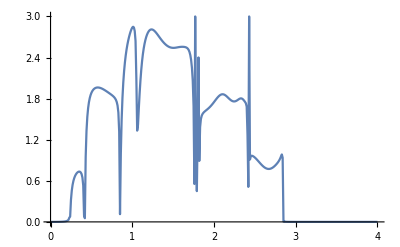

```mathematica
ListPlot[%1190,Joined->True]
```

```mathematica
κκκ[B_,P_,Q_,R_,S_]:=Show[Show[Plot[x=m1[[B*100+1,2]],{x,4,16},PlotStyle->Red],ListLinePlot[Lmean[B,0.5],PlotStyle->Red,PlotTheme->"Detailed"],PlotRange->All],Show[Plot[x=m1[[P*100+1,2]],{x,4,16},PlotStyle->Orange],ListLinePlot[Lmean[P,0.5],PlotStyle->Orange,PlotTheme->"Detailed"],PlotRange->All],Show[Plot[x=m1[[Q*100+1,2]],{x,4,16},PlotStyle->RGBColor[0,1,0]],ListLinePlot[Lmean[Q,0.5],PlotStyle->RGBColor[0,1,0],PlotTheme->"Detailed"],PlotRange->All],Show[Plot[x=m1[[R*100+1,2]],{x,4,16},PlotStyle->RGBColor[0,0,1]],ListLinePlot[Lmean[R,0.5],PlotStyle->RGBColor[0,0,1],PlotTheme->"Detailed"],PlotRange->All],Show[Plot[x=m1[[S*100+1,2]],{x,4,16},PlotStyle->RGBColor[0.5,0.5,0.5]],ListLinePlot[Lmean[S,0.5],PlotStyle->RGBColor[0.5,.5,0.5],PlotTheme->"Detailed"],PlotRange->All],PlotRange->All]
```

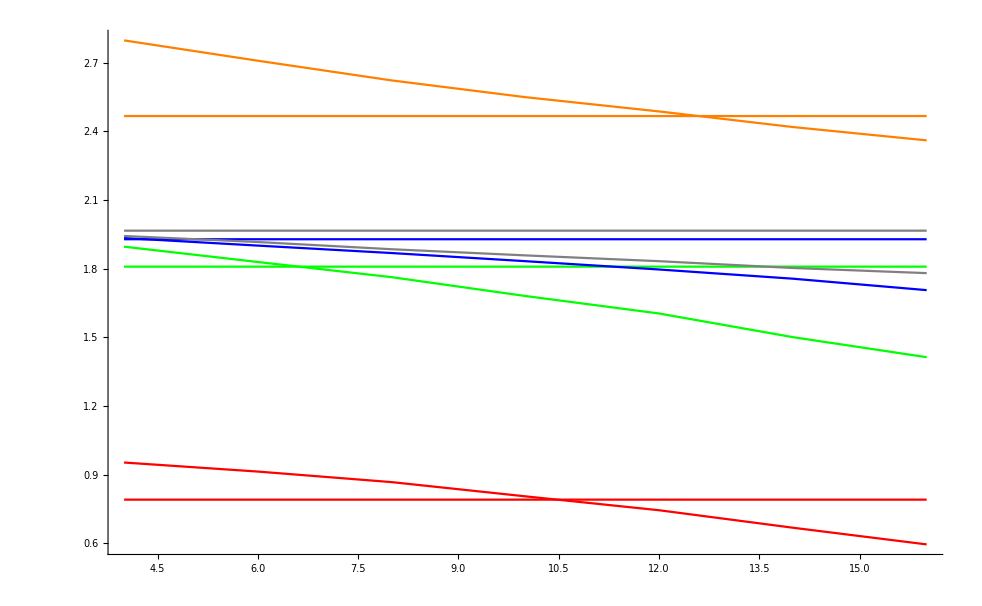

```mathematica
κκκ[.3,1.4,0.5,0.6,0.7]
```

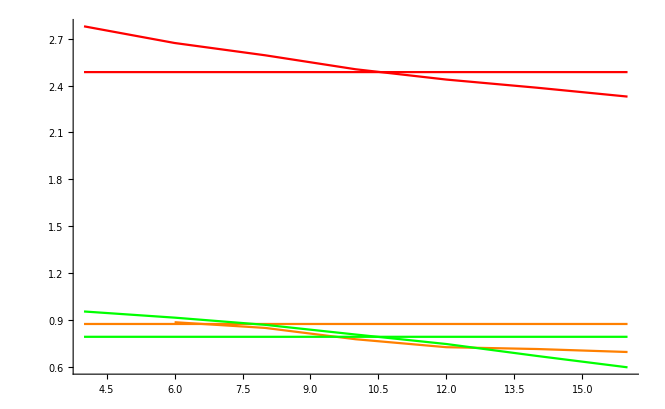

```mathematica
κκκ[1.5,2.5,0.3]
```

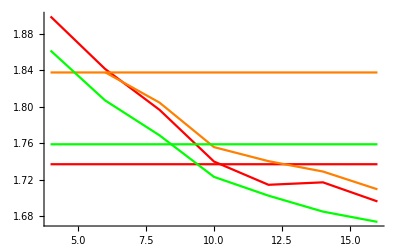

```mathematica
κκκ[2,2.1,2.2]
```

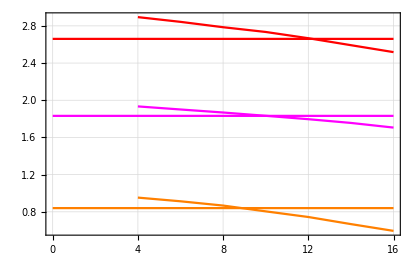

```mathematica
Show[%1031,%1033,PlotRange->All]
```

```mathematica
Show[ListLinePlot[Lmean[0.3,0.5],PlotStyle->Red],ListLinePlot[Lmean[.2,0.5],PlotStyle->RGBColor[RandomReal[{0,0.5}],0.64,RandomReal[{0.5,0.8}]]],ListLinePlot[Lmean[0.5,0.5],PlotStyle->Green],ListLinePlot[Lmean[1,0.5],PlotStyle->RGBColor[RandomReal[{0,0.5}],0.64,RandomReal[{0.5,0.8}]]],ListLinePlot[Lmean[0.6,0.5],PlotStyle->Orange]]
```

-Graphics-

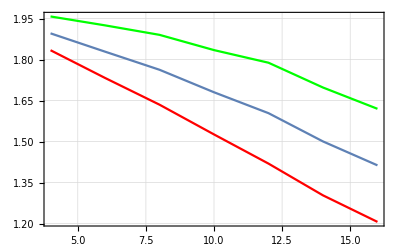

```mathematica
λ[0.5,0.5]
```

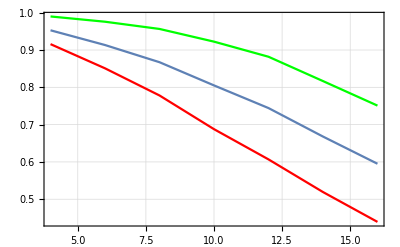

```mathematica
λ[0.3,0.5]
```

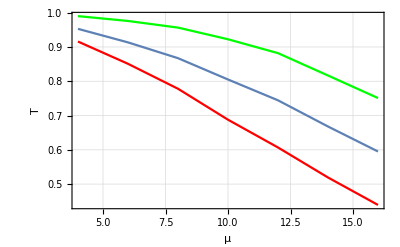

```mathematica
Show[%917,FrameLabel->{{HoldForm[T],None},{HoldForm[μ],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

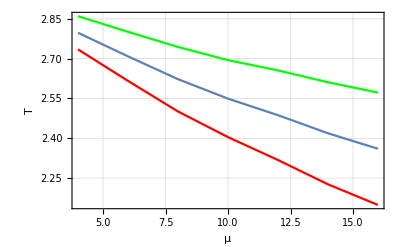

```mathematica
λ[1.4,0.5]
```

```mathematica
Manipulate[λ[ω,0.5],{ω,Range[0.2,3,0.2]}]
```

```mathematica
Export["points.avi",%1116]
```

points.avi

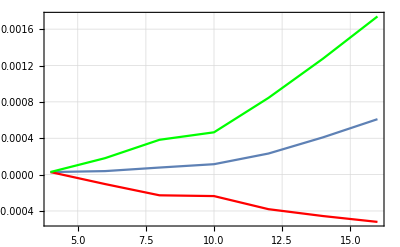

0

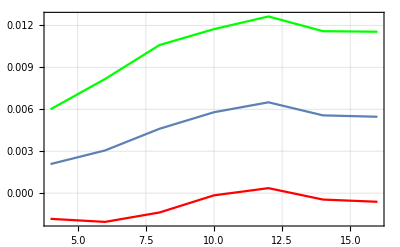

0.2

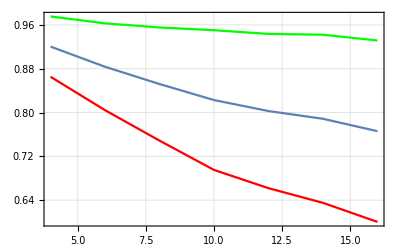

0.4

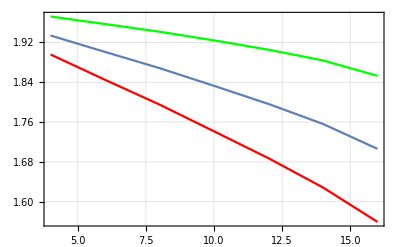

0.6

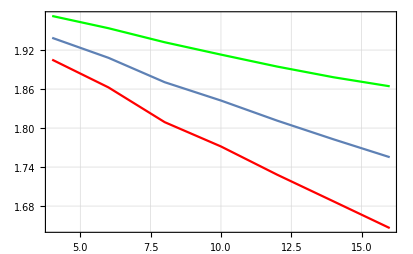

0.8

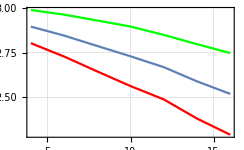

1.

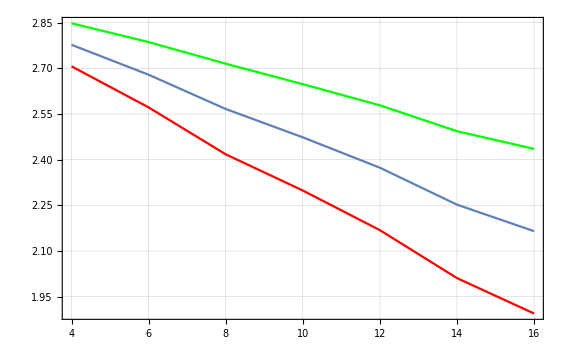

1.2

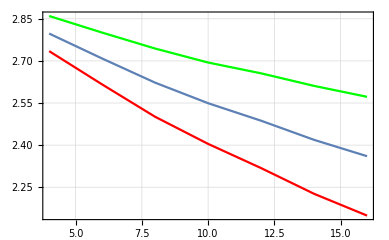

1.4

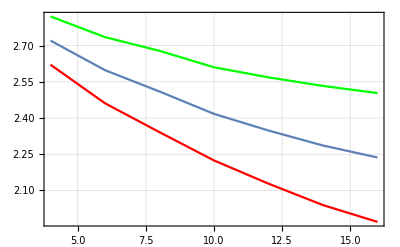

1.6

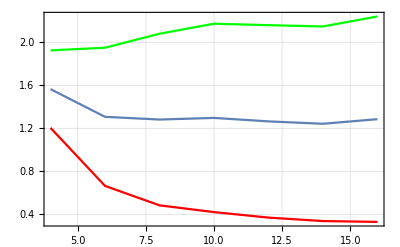

1.8

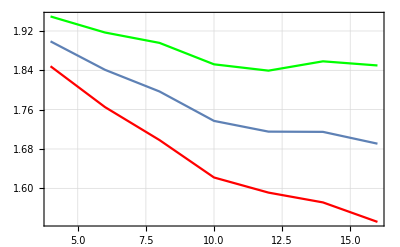

2.

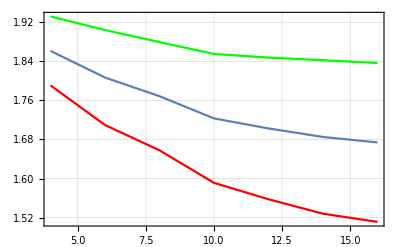

2.2

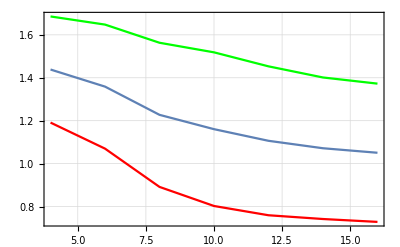

2.4

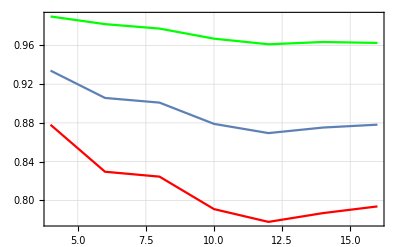

2.6

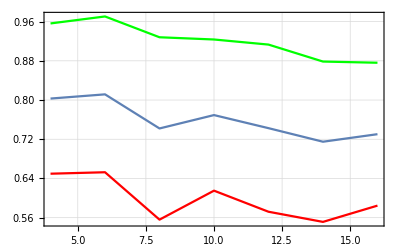

2.8

```mathematica
For[i=0,i<3,i+= 0.2,Print[λ[i,0.5]];Print[i]]
```

```mathematica
ξ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ξ2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ξ3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ξ4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ξ5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ξ6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ξ7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
k77[ω_,ϵ1_]:=k77[ω,ϵ1]=Append[{},Table[ξ7[ω,0.001,1,0,ϵ1],{i,1000}]];
k76[ω_,ϵ1_]:=k76[ω,ϵ1]=Append[{},Table[ξ6[ω,0.001,1,0,ϵ1],{i,1000}]];
k75[ω_,ϵ1_]:=k75[ω,ϵ1]=Append[{},Table[ξ5[ω,0.001,1,0,ϵ1],{i,1000}]];
k74[ω_,ϵ1_]:=k74[ω,ϵ1]=Append[{},Table[ξ4[ω,0.001,1,0,ϵ1],{i,1000}]];
k73[ω_,ϵ1_]:=k73[ω,ϵ1]=Append[{},Table[ξ3[ω,0.001,1,0,ϵ1],{i,1000}]];
k72[ω_,ϵ1_]:=k72[ω,ϵ1]=Append[{},Table[ξ2[ω,0.001,1,0,ϵ1],{i,1000}]];
k71[ω_,ϵ1_]:=k71[ω,ϵ1]=Append[{},Table[ξ1[ω,0.001,1,0,ϵ1],{i,1000}]]
```

```mathematica
ρ7[ω_,ϵ1_]:=Join[Mean[k71[ω,ϵ1]],Mean[k72[ω,ϵ1]],Mean[k73[ω,ϵ1]],Mean[k74[ω,ϵ1]],Mean[k75[ω,ϵ1]],Mean[k76[ω,ϵ1]],Mean[k77[ω,ϵ1]]]
```

```mathematica
MeanDeviation[ρ7[0.5,0.5]]
```

0.157342

```mathematica
γ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
k88[ω_,ϵ1_]:=k88[ω,ϵ1]=Append[{},Table[γ[ω,0.001,1,0,ϵ1],{i,5000}]]
```

```mathematica
ρ8[ω_,ϵ1_]:=Mean[k88[ω,ϵ1]]
```

```mathematica
Timing[Mean[ρ8[0.45,0.5]]]
```

{44.7297,1.04378}

```mathematica
StandardDeviation[ρ8[0.5,0.5]]
```

0.206856

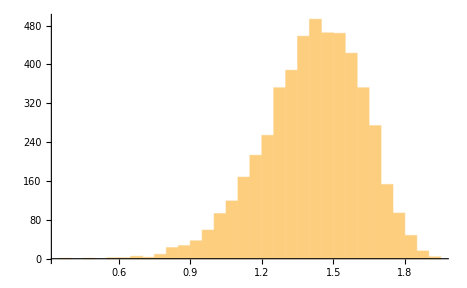

```mathematica
Histogram[%584]
```

```mathematica
Length[%584]
```

5000

```mathematica
Table[γ[0.5,0.001,1,0,0.5],{i,5000}]
```

{1.30123,1.26876,1.6299,1.49601,1.5426,1.22363,1.76845,1.04976,1.58788,1.1871,1.66961,1.55521,1.27064,1.36388,1.16021,1.1521,1.65481,1.1728,1.39615,1.37401,1.55201,1.68762,1.75215,1.2712,1.26094,1.74746,1.33618,1.03889,1.04729,1.51156,1.22447,1.27944,1.30925,1.51846,1.44623,1.79741,1.67522,1.01308,1.58585,1.5208,1.26176,1.26183,1.85933,1.60278,1.61685,1.28843,1.61537,1.42365,1.47868,1.61283,1.61547,1.27832,1.11846,1.47811,1.52518,1.44022,1.12245,1.34096,1.1337,1.49455,0.723643,1.57462,1.48686,1.2502,1.43661,1.59652,1.72375,1.50682,1.516,1.43778,1.02088,1.35195,1.41007,1.41231,1.43231,1.77068,1.0901,1.76729,1.21403,1.20473,1.19087,1.47753,1.2942,1.2964,1.52963,1.65294,1.56542,1.7319,1.63465,1.22241,1.21755,1.33306,1.81981,1.39667,1.35384,1.23733,1.31454,1.19169,1.35355,1.44845,1.60778,1.42918,1.54454,1.46725,1.23263,1.51797,1.66187,1.84667,1.41836,1.62807,1.44319,1.26445,1.64896,1.18126,1.17537,1.17468,1.54972,1.78965,1.61828,1.18931,1.09834,1.58429,1.54165,1.60029,1.30622,1.40764,1.37331,1.1603,1.11834,1.25335,1.43264,1.43227,1.45767,1.51192,1.63216,1.30873,1.15799,1.16106,1.49095,1.42956,1.51159,1.16255,1.39691,1.55084,1.34393,1.21749,1.38387,1.50552,1.67086,1.59113,1.63281,1.13045,1.408,1.47088,1.39545,1.14248,1.6023,1.50225,1.26045,1.37217,1.31231,1.62628,1.71078,1.43681,1.29493,1.55436,1.36853,0.929011,1.19076,1.62009,1.85172,1.20957,1.25422,1.11337,1.33183,1.23393,0.83936,1.62741,1.23867,1.61142,1.27375,1.41748,1.11931,1.3204,1.51599,1.6584,1.38802,0.664143,1.63261,1.28214,1.6709,1.55031,0.886066,1.09217,1.14791,1.42384,1.23538,0.672472,1.6066,1.61064,1.53299,1.36738,1.38644,1.72352,1.41407,1.61075,1.25537,1.51663,1.34305,1.33933,1.58454,1.32621,1.19079,1.08441,1.73077,1.30136,1.13082,0.979654,1.25112,1.39913,1.25504,1.23707,1.60553,1.34958,1.5471,1.32638,1.54904,1.22749,1.65666,1.29393,1.70313,1.45341,1.4963,1.55578,1.68968,1.46293,1.69115,1.20792,1.26054,1.54973,1.69884,1.52319,1.45813,1.5785,1.75953,1.47772,1.36223,1.38385,1.53279,1.65952,1.16196,1.26572,1.49779,1.52508,1.68925,1.13174,1.35401,1.75859,1.30662,1.48011,1.37919,1.50935,1.58082,1.22267,1.58334,1.27584,1.38685,1.27033,1.32009,1.55624,1.57394,1.40479,1.32744,0.929951,1.55943,1.54624,1.31037,1.22212,1.55079,1.57375,1.57364,1.40441,1.36818,1.57531,1.59007,1.53794,1.36817,1.64696,1.59786,1.68056,1.44049,1.27588,1.48663,1.43925,1.33288,1.62908,1.38068,1.57459,1.09418,1.19831,1.52616,1.59404,1.0648,1.52773,1.42432,1.70199,1.75735,1.36926,1.64654,1.41581,1.36987,1.13018,1.64371,1.53729,1.19751,1.10962,1.57995,1.62586,1.37205,1.78667,1.48121,1.53748,1.5761,1.47305,1.59226,1.50032,1.3778,1.32926,1.48222,1.3043,1.39173,1.69746,1.41768,1.24672,1.41452,1.56748,1.51806,1.31199,1.13536,1.11992,1.35669,1.34381,1.57121,1.10079,1.55993,1.49292,1.51259,1.33539,0.999399,1.42871,1.17142,1.59685,1.06514,1.31038,1.26743,1.43321,1.64237,1.12195,1.61878,1.69172,1.8292,1.58247,1.34684,1.71614,1.02862,1.36284,1.34606,1.4126,1.49858,1.42983,1.1975,1.2476,1.72315,1.35485,0.958618,1.50236,1.75437,1.4379,1.3616,1.58395,1.47079,1.495,1.64238,0.922325,1.34758,1.36823,1.47055,1.44783,1.72469,1.51606,1.53128,1.62404,1.59846,1.21601,1.454,1.49023,1.34412,1.71811,1.38007,1.55074,1.33727,1.42543,1.65716,1.74726,1.01481,1.25757,1.33558,1.26524,1.45917,0.788884,1.41616,1.28707,1.44311,1.22233,1.42342,1.58323,1.74703,1.41968,1.2135,1.18585,0.90392,1.38084,1.6787,1.37728,1.57749,1.40218,1.39501,1.3904,1.55868,1.51591,1.2181,1.59663,1.35404,1.43936,1.12965,1.35394,1.27724,1.09974,1.38242,1.17937,1.39404,1.43053,1.46562,1.35953,1.36314,1.12855,1.36323,1.35903,1.34069,1.47435,1.0689,1.55702,1.1019,1.41499,1.42181,1.39669,1.24285,1.27512,1.14086,1.05443,1.41098,1.46154,1.53613,1.80842,1.48745,1.61249,1.33036,1.71549,1.39638,1.32661,1.55862,1.23809,1.4435,1.63542,1.58737,1.52177,1.77803,1.41752,1.46366,1.37601,1.17681,1.06994,1.52132,1.77898,1.38657,1.63745,1.63328,1.46719,1.32764,1.27556,1.23758,1.57153,1.48767,1.33558,0.915386,1.44482,1.83461,1.5821,1.51569,0.760489,1.30364,1.23095,1.24334,1.39014,1.17871,1.47301,1.34346,1.63916,1.49133,1.5373,1.392,1.51659,1.21135,1.15969,1.21481,1.7976,1.70868,1.36718,1.40389,1.24817,1.25232,1.64526,1.2424,1.02621,1.45391,1.75304,1.65826,1.22075,1.5171,1.60165,1.38586,1.32736,1.25654,1.37769,1.51439,1.3284,1.38416,1.28399,1.0761,1.4532,1.52383,1.66068,1.16005,1.52343,1.78876,1.58773,1.48344,1.20931,1.44127,1.59345,1.7505,1.7385,1.0624,1.32332,0.77972,1.40109,1.54273,1.4324,1.45384,1.47819,1.37228,1.466,1.46551,1.46757,1.22324,1.60525,1.389,1.55936,1.72935,1.63062,1.54688,1.40693,1.41865,1.55679,1.09271,1.62707,1.58735,1.63215,1.0912,1.36485,1.22778,1.36695,1.59586,1.34071,1.25832,1.37377,1.23295,1.33589,1.6305,1.22873,1.55718,1.40871,1.47158,1.49009,1.08972,1.44172,1.37971,0.99443,1.306,1.74183,1.86704,1.4669,1.45201,0.926635,1.16949,1.17574,1.25985,1.4301,1.39227,1.52555,1.68104,1.46905,1.33088,1.29468,1.37439,1.84526,1.66727,1.41037,1.47682,1.55934,1.49466,1.22404,1.34462,1.28791,0.94436,1.01702,1.47954,1.25905,1.26112,1.37624,1.74918,1.57223,1.21575,1.37792,1.58273,1.30843,1.47385,1.4088,1.37326,1.22986,1.20818,1.37154,1.13837,1.22452,1.58182,1.74919,1.11268,1.31237,1.56132,0.823768,1.44605,1.52086,1.23708,1.22881,1.48661,1.62618,1.56848,1.26626,1.04628,1.20094,1.44863,1.75676,1.38871,1.13259,1.73473,1.48614,1.5797,1.42473,1.45717,1.06459,1.24664,1.0795,1.54138,1.27714,1.48889,1.45647,1.4795,1.35271,1.53381,1.5559,1.52957,1.60346,1.40654,1.72119,0.926738,1.51361,0.883397,1.45625,1.36247,1.2796,1.37694,1.08257,1.0764,1.69302,1.58587,1.18248,1.56943,1.34314,1.42489,1.47945,1.3974,1.50211,1.09359,1.3748,1.34155,1.29349,0.810594,1.09234,1.42115,1.50051,1.66724,1.33838,1.72253,1.45429,1.57622,1.61095,0.948266,1.68917,1.57728,1.62421,1.4796,1.05092,1.58785,1.64519,1.54906,1.5044,1.33994,1.18489,1.70723,1.7687,1.31226,1.61053,1.25899,0.91007,0.838708,1.44765,1.27213,1.48682,1.59796,1.50742,1.43167,1.29082,1.56107,1.26584,1.36994,1.34991,1.58394,1.01271,1.57161,1.53591,1.75313,1.64813,1.70429,1.72462,1.49208,1.45782,0.98681,1.57767,1.42618,1.57003,1.25195,1.44963,1.42309,1.35871,1.46508,1.58955,1.48345,1.11108,1.5083,1.21017,1.12631,1.29674,1.36006,1.33917,1.2703,1.21921,1.62367,1.5723,1.28161,1.53242,1.53575,1.51691,1.72955,1.14041,1.5343,1.13063,1.44944,1.47829,1.66193,1.68417,1.34621,1.13449,1.54777,1.37318,1.08145,0.904081,1.05743,1.47797,1.47344,1.34442,1.51575,1.42913,1.12168,1.69071,1.45055,1.51018,1.72613,1.5074,1.26027,1.06347,1.36829,1.34482,1.62853,1.34468,1.49358,1.59898,1.31462,1.56746,0.864757,1.57194,1.84581,1.1974,1.59867,1.39967,1.56134,1.42574,1.27316,1.62913,1.69144,1.52935,1.1649,1.60954,1.34481,1.35526,1.48194,1.64986,1.48326,1.24447,1.16814,1.40632,1.80992,1.34706,1.50217,1.59041,1.66242,1.71842,1.77542,1.1818,1.51817,1.35464,1.36171,0.912432,1.80184,1.15383,1.40329,1.52632,1.55195,1.48941,1.26974,1.29567,1.53278,1.40838,1.43899,1.791,1.06267,1.24049,1.65603,1.49504,1.38096,1.18553,1.13601,1.56931,1.75587,1.4041,1.33658,1.19974,1.26081,1.07477,1.66351,1.40243,1.57895,1.45457,1.58721,1.29523,1.14943,1.63923,1.16897,1.32158,1.59402,1.49297,1.64447,1.36671,1.47597,1.40428,1.15677,1.74105,1.49718,1.57489,1.41417,1.43084,1.25375,1.43871,1.48815,1.21101,1.3892,1.46302,1.56922,1.68004,1.2065,1.36951,1.54749,1.46347,1.26841,1.32767,1.55014,1.29502,1.58205,1.69755,1.44567,1.19898,1.46964,0.996911,1.59889,1.7484,1.68625,1.22784,1.37744,1.49487,1.39204,1.1507,1.23537,1.40925,1.38413,1.32612,1.63704,1.19204,1.53158,1.13016,1.39434,1.37581,1.75849,1.51255,1.64015,1.52423,1.39306,1.33795,1.5681,1.32747,1.77924,1.86921,1.45252,1.52653,1.42218,1.64326,1.77264,1.68211,1.1443,1.71858,1.68588,1.21095,1.40015,1.27642,1.20347,1.04698,1.23129,1.47404,1.35429,1.10778,1.60046,1.16481,1.34183,1.73931,1.5183,1.81942,1.34714,1.12282,1.3079,1.314,1.28618,1.57768,1.60734,1.63591,1.66401,1.75496,1.44437,1.64318,1.30311,1.32104,1.67806,1.24556,1.50019,1.78851,1.23256,1.05617,1.82567,1.4011,1.31058,1.23958,1.41876,1.00855,1.5744,1.72622,1.0874,1.69789,1.76971,1.39689,1.41012,1.46783,1.29528,1.38718,1.33314,1.11623,1.72961,1.24095,1.67071,1.26448,1.50419,1.49775,1.3404,1.14595,1.5374,1.52842,1.61679,1.5881,1.42752,1.34652,1.18974,1.62647,1.0306,1.41433,1.03507,1.59025,1.43504,1.47952,1.42405,1.64413,1.69692,1.26403,1.33028,1.37344,1.49402,1.06125,1.2874,1.50425,1.61728,1.15895,1.28306,1.59705,1.08008,1.88843,1.15808,1.39542,1.63074,1.63059,1.61262,1.01966,1.48409,0.991435,1.44399,1.26347,1.47303,1.0169,1.43648,1.34679,1.20712,1.67065,1.66371,1.22803,1.57499,1.01871,1.60777,1.51742,1.59326,1.34635,1.29092,1.49385,1.13131,1.45869,1.4895,1.40832,1.72184,1.54057,1.4785,1.24339,1.70497,1.45505,1.33936,1.054,1.20123,1.50917,1.65769,1.26836,1.60047,1.35252,1.48465,1.28991,1.48532,1.24204,1.24101,1.44949,1.42441,1.67264,1.6661,1.58432,1.35965,1.61358,1.57689,1.44087,1.20892,1.67843,1.63401,1.38858,1.43982,1.38738,1.06581,1.27319,1.25027,1.12105,1.36862,1.34345,1.59577,1.19882,1.25029,1.53894,0.970347,1.22553,1.36563,1.24293,1.45624,1.20287,1.37036,1.27412,1.7904,1.40267,0.963298,0.885472,1.40316,1.44542,1.27553,1.51799,1.26537,1.59617,1.15172,1.63541,1.47518,1.21951,1.6335,1.47482,1.51096,1.45558,1.63364,1.61318,1.46406,1.39255,1.45525,1.43783,0.856541,1.74477,1.18716,1.57633,1.40351,1.45959,1.59699,1.6302,1.69889,1.3295,1.34883,1.71597,1.15429,1.38579,1.33372,0.758106,1.70839,1.89768,1.75037,1.32569,1.71557,1.39132,1.81026,1.09116,1.66558,1.37073,1.24536,1.6481,1.49783,1.60412,1.61138,1.65398,1.49849,1.6309,1.7279,1.35019,1.54185,1.3941,1.67832,1.63411,1.52902,1.60509,1.14635,1.60677,1.52623,1.63033,1.66684,1.53617,1.46274,1.59723,1.59564,1.15167,1.72301,1.27755,1.61702,1.32334,1.27653,1.80376,1.17914,1.47901,1.5701,1.52065,1.61527,1.21555,1.39487,1.82892,1.18155,1.08778,1.77799,1.71354,1.26953,1.8179,1.54459,1.30016,1.15676,1.40095,1.22346,1.82472,1.35159,1.51444,1.3395,1.56199,1.62414,1.56113,1.46263,1.26753,1.5046,1.77031,1.55242,1.03311,1.0131,1.33669,1.64081,1.18283,1.34492,1.5705,1.61257,1.25945,1.29133,1.68862,1.25824,1.18085,1.59966,1.08472,1.3571,1.51238,1.54737,1.62785,1.04318,1.33174,1.03749,1.47327,1.47722,1.39211,1.59188,1.71201,1.47528,1.6078,1.58069,0.902222,1.34913,1.69532,1.44619,1.49528,1.36325,1.25894,1.48505,1.47971,1.46552,1.55381,1.49057,1.39889,1.52973,1.40509,1.6212,1.71785,1.6187,1.64524,1.2621,1.63683,1.30391,0.863532,1.43116,1.16847,1.45873,1.39205,1.6345,1.33366,1.30283,1.28996,1.56021,1.31734,1.52595,1.57922,1.44139,1.79335,1.40127,1.57652,1.4779,1.1237,1.43309,1.59669,1.40638,1.28431,1.53829,1.47951,1.50618,1.02558,1.23884,1.37,1.41643,1.67267,1.55086,0.874349,1.36,1.57962,1.5314,1.30018,0.823889,1.45911,1.62918,1.25544,1.14719,1.60298,1.51263,1.55397,1.56054,1.61211,1.52144,1.45376,1.19141,1.63703,1.57395,1.18963,1.61367,1.38487,1.35862,1.62356,1.33367,1.41023,1.2307,1.62126,1.41572,1.28433,1.23358,1.25325,1.42549,1.4734,1.08881,1.13057,1.52332,1.31384,1.2533,1.31427,1.3702,1.46919,1.39571,1.47568,1.56507,1.57004,1.49743,1.31114,1.46077,1.84013,1.28145,0.996251,1.45716,1.30643,1.19822,1.65532,1.74462,1.32454,1.7969,1.5428,1.58462,1.58576,1.37039,1.21309,0.949534,1.69695,1.42351,1.34091,1.64055,1.25524,1.1535,1.61276,1.70536,1.43124,1.68741,1.01845,1.34962,1.32245,1.52222,1.37702,1.4093,1.72376,1.27781,1.02962,1.18572,1.11121,1.74278,1.77812,1.70033,1.62664,1.31912,1.45237,1.19214,1.36465,1.50611,1.50947,1.60881,1.58197,1.60602,1.37788,1.55864,1.36875,1.33899,1.68275,1.70905,1.68971,1.34586,1.11256,1.51352,1.31334,1.23107,1.5373,1.2967,1.49045,1.15988,1.3089,0.816967,1.74775,1.46474,1.48506,1.33565,1.64782,1.59351,1.14835,1.36289,1.52956,1.15423,1.78475,1.35107,1.24022,0.929704,1.52163,1.28157,1.51517,1.47041,1.21805,1.46152,1.64808,1.49099,1.54378,1.0315,1.4258,1.30559,1.66587,1.18501,1.19176,1.66321,1.28081,1.58765,1.77501,1.08481,1.34485,1.46221,0.984899,1.356,1.52439,1.28572,1.55338,1.55864,1.55507,1.5554,1.41504,1.56921,1.57749,1.43646,1.24883,1.6558,1.14944,1.38399,1.31485,1.76512,1.69612,1.40602,1.44051,1.4525,1.42239,1.52695,1.90957,1.56678,1.07518,1.44639,1.16768,1.42802,1.42661,1.38671,1.38576,1.32142,0.975074,1.6839,1.27111,1.181,1.0891,0.899388,1.51026,1.64663,1.49607,1.33663,1.77693,1.52921,1.00421,1.58941,1.64569,1.18092,1.383,1.33075,1.69402,1.13707,1.39441,1.68815,1.42562,1.33135,1.16127,1.44262,1.7619,1.64201,1.39446,1.54797,1.21314,1.48305,1.59228,1.7219,1.33368,0.931822,1.53796,1.30973,1.65637,1.21771,1.42928,1.18391,1.07625,1.72249,1.7149,1.53564,1.32403,1.56144,1.58729,1.35653,1.39211,1.61385,1.4682,1.36616,1.35183,1.51415,1.3998,1.78631,1.60617,1.35058,1.52098,1.52973,1.16536,1.16342,1.41391,1.34629,1.47183,1.1473,1.6116,1.61402,1.65043,1.51301,1.29135,1.52228,1.79548,1.54912,1.54537,0.93353,1.32785,1.65978,1.58271,1.50862,1.14461,1.24423,1.65113,1.76152,1.52475,1.70081,1.42662,1.33576,1.7385,1.33585,1.47075,1.601,1.73824,1.483,1.64463,1.30734,1.6457,1.6192,1.47824,1.25323,1.52352,1.58292,1.31164,1.64605,1.55006,1.57689,1.44333,1.16833,1.61384,1.51645,1.65718,1.47292,1.50845,1.4537,1.30097,1.61536,1.54972,1.24311,1.48719,0.982301,1.55202,0.941397,1.55763,1.2612,1.12182,0.970799,1.29504,1.51327,1.36819,1.28196,1.64888,1.52531,1.7581,1.31061,1.12135,1.57639,1.09069,1.38798,1.70615,1.71553,1.35537,1.18827,1.39791,1.23725,1.37676,1.12776,1.18846,0.361018,1.38835,1.31516,1.56998,1.28935,1.44938,1.58851,1.18799,1.22421,0.653299,1.63321,1.16798,1.57042,0.915384,1.74888,1.67283,1.62117,1.81764,1.62083,1.15645,1.52595,1.68505,1.5113,1.41256,1.66248,1.28374,1.38595,1.37524,1.50588,1.59754,1.56727,1.65573,1.42648,1.10257,1.43389,1.12573,1.61218,1.4042,1.28495,1.44474,1.19793,1.59287,1.52507,1.61593,1.8068,1.06212,1.37468,0.976148,1.19933,1.60463,1.61126,1.25188,1.55483,1.34018,1.29026,1.41071,1.29771,1.66616,1.41524,0.852361,1.19792,1.6536,1.27239,0.81146,1.16196,1.11294,1.5615,1.55604,1.29859,1.52534,1.13615,1.06183,1.55465,1.45907,1.38749,1.45943,1.415,0.969557,0.869015,1.52361,1.35459,1.21663,1.53015,1.79413,1.40763,1.4904,1.20418,1.66866,1.08368,1.64343,1.78043,1.44758,1.5406,1.55097,1.01777,1.03234,1.46658,1.32074,1.41468,1.16851,1.45326,1.47269,1.11666,1.48473,1.66647,1.61147,1.68631,1.57256,1.4605,0.886525,1.58082,1.07602,1.24646,1.42118,1.50035,1.34636,1.64659,1.78141,1.21699,1.09612,1.557,1.0548,1.65247,1.43929,1.35837,1.27971,1.02243,1.28842,1.37204,1.41391,1.76094,1.4133,1.26724,1.77824,1.50704,1.34552,1.71034,1.1551,1.3806,1.46752,1.58878,1.49926,1.60308,1.37382,1.63633,1.07168,1.82884,1.60667,0.922268,1.33776,1.42493,1.11013,1.53245,1.55043,1.5651,1.19936,1.17499,1.39037,1.29914,1.74229,0.855022,1.75651,0.536535,1.27751,1.71915,1.70364,0.949355,1.83767,1.44184,1.6595,1.41334,1.74839,1.53976,1.84821,1.44154,1.45093,1.20788,1.54084,1.70575,1.37064,1.5306,1.68351,1.66087,0.910743,1.32951,1.19211,1.28149,0.777479,1.44533,1.72889,1.3613,1.0894,1.342,1.24709,0.912752,1.45252,1.49631,1.75411,1.64189,1.71449,1.23701,1.27408,1.7202,1.16813,1.26836,1.51607,1.31986,1.44471,1.64738,1.4632,1.50036,1.26336,1.33565,1.50295,1.46385,1.30331,1.52037,1.59624,1.63035,1.62661,1.60187,1.07385,1.29104,1.28544,1.2307,0.980275,1.38558,1.27835,1.50898,1.34871,1.23184,1.56799,1.52235,1.54051,1.04436,1.60555,1.49903,1.56979,1.07745,0.783979,0.953716,1.53037,1.22788,1.64031,1.25963,1.62113,1.46927,1.32378,1.67886,1.28627,1.82135,1.50294,1.35488,0.412701,1.30492,1.43631,1.38112,1.61071,1.45951,1.43359,1.73394,1.15032,1.19691,1.55558,1.55943,1.24735,1.6024,1.4205,0.848121,1.45598,1.4397,1.32548,1.26756,1.445,1.22575,1.54206,1.25339,1.30033,1.15007,1.44308,1.50512,1.47214,1.47887,1.43406,1.46389,1.55539,1.15197,1.56805,1.46744,1.26114,1.11239,1.32015,1.80525,1.53626,1.58652,1.67938,1.476,1.67926,1.48638,1.4502,1.50417,0.946293,1.42654,1.66035,1.36499,1.41433,1.37092,1.31584,1.58865,1.39508,1.4853,1.49421,1.53179,1.6559,1.29666,1.50948,1.51024,1.03398,1.66257,1.24981,1.80369,1.2924,1.14399,1.56651,1.52787,1.3453,1.61258,1.46979,1.82529,1.19982,1.66762,1.06912,1.29719,1.77416,1.64475,1.68183,0.978174,1.62192,1.53727,1.31853,1.47204,1.50502,0.9774,1.48035,1.53127,1.39174,1.53012,1.728,1.61891,1.40497,1.00382,1.57816,1.45287,1.51156,1.22855,1.48789,1.25655,1.59855,1.58762,1.2603,1.35213,1.22313,1.69992,1.35219,1.39621,1.24626,1.62896,1.65958,1.41335,1.23753,1.30961,1.45108,1.45775,1.51977,1.65413,1.44495,1.11936,1.41257,1.53488,1.39788,1.46016,1.20064,1.58787,1.3859,1.46706,1.46685,1.20527,1.36559,1.57213,1.59848,1.24991,1.59972,1.50226,1.56631,1.52102,1.0642,1.35878,1.27687,1.4234,1.16339,1.58738,1.59594,1.61511,1.47823,1.11886,1.37583,1.17315,1.39097,1.24249,1.07693,1.3924,1.31595,1.55943,1.42305,1.66772,1.68793,1.64189,1.45644,1.42721,1.68014,1.55714,1.34347,1.16644,1.4666,1.25679,1.54195,1.11162,1.28437,1.54288,1.45616,1.45089,1.44141,0.882253,1.58599,1.62823,1.38032,1.63305,1.22977,1.73072,1.32017,1.59896,0.80963,1.5435,1.35729,1.38268,1.59391,1.90913,1.49792,1.29662,1.14437,1.41558,1.4617,1.22067,1.18078,0.92818,1.45684,1.33688,1.32315,1.44858,1.40228,1.51781,1.46258,1.39882,1.75071,1.52717,1.46177,1.39756,1.16064,1.65269,1.41484,1.18759,0.928367,1.19029,1.44794,1.59364,1.25434,1.64862,1.15452,1.15698,1.44294,1.67404,1.54689,1.31126,0.928154,1.74383,1.46277,1.66999,1.46818,1.40458,1.51516,1.59464,1.67533,1.16967,1.50843,1.42474,1.72871,1.61917,1.30351,1.06888,1.2679,1.47176,1.30809,1.47844,1.58425,1.08738,1.33501,1.51368,1.18187,1.67805,1.57247,1.40255,1.20808,1.75055,1.50174,1.49655,1.52084,0.889794,1.2847,1.26105,1.68147,1.70535,1.7065,1.5718,1.80295,1.80926,0.977429,1.64365,1.6423,1.46986,1.51374,1.57607,1.12048,1.48726,1.71993,1.27832,1.46988,1.38291,1.4553,1.40627,1.03523,1.68475,1.47213,1.52334,1.09938,1.32058,1.43255,1.58246,1.58608,1.22729,1.31607,1.04158,1.38412,1.40726,0.758837,1.42061,1.70104,1.20612,1.52299,1.50126,1.35717,1.44929,1.4408,1.59639,1.61373,1.47354,1.28658,1.44263,1.28097,1.0829,1.52617,1.23469,1.60467,1.3925,1.39032,1.55801,1.75059,1.85755,1.34433,1.32371,1.49018,1.41378,1.28125,1.52606,1.34736,1.69255,1.37729,1.54362,1.61697,1.24119,0.870121,1.47218,1.75112,1.27305,1.745,1.16838,1.24237,1.59467,1.27206,1.0135,1.58537,1.3505,1.67864,1.41149,1.36794,1.47354,1.32536,1.30107,1.73906,1.44625,1.32378,0.895306,1.14427,1.72429,1.34078,1.70083,1.29625,1.00477,1.37444,1.30259,1.26433,1.29221,1.53026,1.36771,1.44162,1.39937,1.58249,1.48558,1.76582,1.70481,1.68362,1.254,1.35086,1.32991,1.13975,1.46221,1.31668,1.70976,1.60525,1.36228,1.25296,1.33537,1.31075,1.42354,0.992882,1.54561,1.19713,1.45019,1.67574,1.74083,1.15319,1.52328,1.20489,1.4868,1.61301,1.67571,1.38752,1.12903,1.40766,1.27397,1.09174,1.58717,1.24795,1.25079,1.43443,1.67938,1.39145,1.81942,1.42875,1.45546,1.50547,1.40941,0.99457,1.37593,1.35994,1.17106,1.41345,1.53684,1.2151,1.43314,1.14269,1.07933,1.30737,1.45125,1.40891,1.51147,1.4229,1.36486,1.83587,1.62548,1.55438,1.28828,1.22611,1.56144,1.39831,1.56789,1.75278,1.31522,1.20464,1.54926,1.0971,0.991922,1.35777,1.61555,1.50513,1.57909,1.12287,1.44296,1.30736,1.41109,1.23669,1.05193,1.44538,1.56702,1.5869,1.38799,1.00645,1.28437,1.50959,1.2361,1.44766,1.58268,1.60391,1.41034,1.32304,1.54977,1.56036,1.40704,1.68867,1.67742,1.44563,1.4596,1.65459,1.53307,1.56998,0.932584,1.60182,0.925362,1.55542,1.45349,1.30143,1.48907,1.08642,1.03741,1.78312,1.78123,1.43765,1.4586,1.64575,1.79606,1.72336,1.51375,1.35611,1.43757,1.34485,1.6355,1.71774,1.54645,1.51429,1.5033,1.52755,1.37014,1.65352,1.71231,1.38635,1.31224,1.57421,1.37099,1.72338,1.62779,1.06619,1.37084,1.52322,1.70388,1.30675,1.69089,1.41365,1.48641,1.57353,1.62487,1.55826,1.19439,1.4252,1.85339,1.57289,1.31739,1.58515,1.31462,1.23224,1.16642,1.39334,1.47832,1.66945,1.45222,1.67908,1.43142,1.69989,1.85173,1.44767,1.39683,1.55283,1.42859,1.47945,1.37715,0.949355,1.36745,1.38423,0.9903,1.32608,1.45648,0.734539,1.3867,1.53543,1.41064,1.24964,1.33569,1.31797,1.29768,0.895056,1.24955,1.27837,1.09763,1.1946,1.29341,1.35645,1.46123,1.61208,1.54468,1.2864,1.36413,1.53889,1.41134,1.35165,1.68232,1.57088,1.56005,1.53856,1.37512,1.20693,1.61828,1.2433,1.50403,1.57414,1.55796,1.42098,1.48888,1.42224,1.75008,1.42636,1.69743,1.57521,1.22158,1.42674,1.58405,1.35391,1.70011,1.40687,1.67503,0.989391,1.58869,0.984174,1.67302,1.36452,1.42329,1.25368,1.3993,1.17895,1.10556,1.47855,1.24646,1.34847,1.48998,1.2747,1.71806,1.55626,1.4771,1.11187,1.16748,1.16945,1.34328,1.55577,1.04617,1.24986,0.914654,1.31385,1.61299,1.4918,1.09974,1.01302,1.4532,1.13,1.13682,1.49771,1.33912,1.38876,1.32165,1.50395,1.48844,1.3459,1.01966,1.68819,1.86945,1.5948,1.34122,1.32036,1.42643,1.19256,1.31328,1.55114,1.54742,1.24284,1.57903,1.40357,1.49051,1.57237,1.29967,1.78008,1.42977,1.13951,1.29168,1.44303,1.66369,1.41845,1.25387,1.57403,1.2555,1.77136,1.77392,1.28609,1.54545,1.15172,1.23898,1.68491,1.71483,1.39441,1.19703,1.55625,1.77452,1.82382,1.49837,1.56414,1.38865,1.3723,1.37296,1.44436,1.43149,1.34005,1.66318,1.3299,1.29843,0.941566,1.42245,1.60369,1.6161,1.37574,1.059,1.29016,1.38337,1.75495,1.60556,1.49553,1.33583,1.30718,1.49286,1.09097,1.3511,1.63997,1.67694,1.63206,1.08632,1.00607,1.38776,1.46645,1.48356,0.838175,0.900375,1.12192,1.36829,1.27132,1.28097,1.31857,1.29925,1.63596,1.45482,1.18297,1.66112,1.42416,1.39851,1.35828,1.01202,1.48547,1.73339,1.75263,1.72001,1.28881,1.36363,1.37284,1.64062,1.14497,1.36634,1.65671,1.44335,1.32399,1.74552,1.47202,1.48738,1.51711,1.22855,1.54629,1.5239,1.63754,1.28068,1.20308,1.2132,1.46864,1.52901,1.74874,1.49504,1.4192,1.51048,1.39484,1.67576,0.844634,1.23216,1.58629,1.54159,1.56743,1.55159,1.2012,1.28266,1.51185,0.856082,1.47723,1.15829,1.34083,1.60319,1.63997,1.72184,1.63147,1.54741,1.45685,1.3713,1.76847,1.38846,1.16957,1.56395,1.44179,1.23296,1.44933,1.30525,1.51035,1.22876,1.5475,1.4357,1.0626,1.38852,0.910963,1.46987,1.30093,1.15926,1.18289,1.51776,1.44552,1.36597,0.960532,1.21902,1.42695,1.53661,1.46911,1.65589,1.39343,1.40671,1.39636,1.77657,1.45114,1.33397,1.9114,1.49156,1.54706,1.16111,1.48044,1.71841,1.54683,1.33355,1.17253,1.67954,1.75097,1.48896,1.31842,1.24217,1.48442,1.45602,1.40648,1.54031,1.50975,1.45041,1.40157,1.65443,1.14992,0.970402,1.18659,1.50576,1.59005,1.24864,1.49908,1.2934,1.18588,1.44134,1.03506,1.48698,1.0492,1.26526,1.43653,1.2295,1.84598,1.60102,1.58752,1.78592,1.1189,1.63214,0.929641,1.37231,1.31948,1.10428,1.48691,1.35875,1.48308,1.06107,1.74369,1.61517,1.6505,1.32139,1.58582,1.48882,1.48492,0.999556,1.71693,1.48321,1.29746,1.6079,1.08973,1.12154,1.68456,1.70252,1.30181,1.48328,1.60483,1.37137,1.34713,1.66234,1.04944,1.24609,1.23975,1.41769,1.31766,1.54478,1.26604,1.06289,1.47743,1.82607,1.14485,1.58324,1.23876,1.69747,1.39206,1.68205,1.47535,1.71542,1.36961,1.3091,1.40052,1.43454,1.02602,1.54424,1.50114,1.42414,1.78117,1.26299,1.49399,1.07408,1.23922,1.38649,1.61528,1.497,1.67727,1.0089,1.49274,1.08134,1.47841,1.72211,1.55638,1.76467,1.23176,1.24783,1.42681,1.38244,1.5025,1.721,1.53559,1.25397,1.52789,1.71826,1.11946,1.68951,1.37655,1.68263,1.36124,1.51896,1.15375,1.7714,1.68448,1.77494,1.70825,0.986158,1.08244,1.6976,1.64585,1.43102,1.22237,1.20202,1.76103,1.63579,1.40237,1.52199,1.51665,1.01544,0.863202,1.62808,1.17479,1.14179,1.62288,1.35358,1.56577,1.66637,1.37833,1.80743,1.28015,1.56172,1.16265,1.51531,1.50611,1.16734,1.24602,1.59749,1.53742,1.27472,1.76213,1.78591,1.47249,1.51933,1.11089,1.48677,1.35609,1.49286,1.3768,1.33007,1.14632,0.97589,1.44048,1.33201,1.46826,1.26183,1.58385,1.45085,1.33187,1.18421,1.42674,1.45947,1.25525,1.46846,1.4816,1.75505,1.55175,0.989499,1.31928,1.45015,1.12724,1.46734,1.32867,1.43967,1.64661,1.75168,1.45427,1.20834,1.55463,1.26638,1.10155,1.39366,1.53125,1.38941,1.40956,1.48801,1.56179,1.34365,1.59585,1.57138,1.37701,1.64827,1.39383,1.12683,1.54764,1.42341,1.79565,1.38786,1.22752,1.28457,1.82607,1.40515,1.10238,1.86644,1.33288,1.49537,1.27022,1.20754,1.68683,1.3456,1.76044,0.888779,1.25891,1.42214,1.63685,1.60558,1.71235,1.6213,1.40892,1.73921,1.29931,1.20088,1.61557,1.56025,1.39169,0.969507,1.81262,0.883254,1.11551,1.53339,1.4419,1.25596,1.2689,1.33417,0.658423,1.7059,1.64863,1.54304,1.5319,1.5534,1.25481,1.47804,1.82704,1.58668,1.46691,1.36584,1.41755,1.25367,1.39069,1.5284,1.00749,1.24002,1.58399,1.35442,1.31232,1.64324,1.2103,1.63985,1.29178,1.25218,1.06337,1.66976,1.13307,0.890804,1.23876,1.69946,1.50457,1.35775,1.11525,1.11095,1.33745,1.413,1.44848,1.36695,1.4055,1.11529,1.70774,1.27636,1.40776,1.28603,1.24017,1.00697,1.40348,1.3274,1.62714,1.26433,1.06574,1.34923,1.11888,1.85269,1.50726,1.4101,1.43023,1.60717,1.57343,1.61624,1.74082,1.33784,1.61701,1.39537,1.49657,1.2608,1.56819,1.35611,1.53624,1.49438,1.58323,1.34676,1.14403,1.15287,1.27689,1.23409,1.27383,1.50453,1.33002,1.70763,1.45859,1.44061,1.51856,1.25413,1.38192,1.38638,1.52812,1.46941,1.32607,1.13354,1.23398,1.33706,1.39175,1.66104,1.43691,1.11284,1.47101,1.31108,1.73631,1.39355,1.40787,1.13891,1.67963,1.1971,1.35953,1.23013,1.4217,1.44406,1.33619,1.13591,1.67293,1.73479,1.49872,1.60889,1.3138,1.49144,1.28552,1.40156,1.22773,1.09314,1.53275,1.60677,1.28284,1.48176,1.39036,1.2207,1.50311,1.45066,1.07025,1.61616,0.709905,1.16835,1.15231,1.48952,1.50004,1.54072,1.60894,1.10858,1.71183,1.3509,1.31741,1.7048,1.39258,1.40469,1.5422,0.764304,1.44269,1.67183,1.32713,1.29718,1.23201,1.5866,1.61639,1.42564,1.81029,1.57248,1.77664,1.26598,1.35445,1.32626,1.60178,1.63959,1.50457,1.47389,1.53531,1.41321,1.05836,1.62393,1.22884,1.3659,1.42613,1.17301,1.67501,1.58094,1.4648,1.36557,1.44647,1.13057,1.48756,1.47712,1.60463,1.45747,1.49426,1.51908,1.41532,1.45433,1.46473,1.27481,1.54722,1.44635,1.45315,1.13418,1.43858,1.47486,1.17944,1.35808,1.48071,1.29398,1.35122,1.70153,1.44504,1.63155,1.23264,1.3339,1.48016,1.7478,1.58886,1.41901,1.2049,1.57652,1.15344,1.67834,1.5239,1.07916,1.46116,1.37129,1.4965,1.71908,1.50049,1.59961,1.49274,1.81891,1.33346,1.72466,1.21337,1.54621,1.55634,1.20533,1.01433,1.04389,1.62211,1.0952,1.59057,1.29191,1.46053,1.62546,1.23211,1.16944,1.35423,1.70275,1.35789,1.65785,1.45578,1.2445,1.3635,1.5048,1.24265,1.13758,1.43904,1.31095,1.4567,1.24666,1.11447,1.48498,1.32425,1.53483,1.50166,1.24468,1.73927,1.35242,1.54098,1.7912,1.5041,1.70096,1.61889,1.22939,1.60678,1.35219,1.89245,1.63468,0.933055,1.66416,1.57346,1.15388,1.11438,1.62056,0.993099,1.24462,1.71049,1.27098,1.48067,1.41305,1.24731,1.60837,1.3963,0.950537,1.27074,1.47115,1.33994,1.42709,1.64153,1.38001,1.41853,1.64215,1.43336,1.20089,1.19467,1.5236,1.10636,1.2936,1.4668,1.08377,0.912037,1.70962,1.23513,1.41743,1.4861,1.77752,1.27669,1.10956,1.38688,0.960377,1.34651,1.46195,1.40765,1.64011,1.35891,1.50954,1.74212,1.75544,1.10165,0.957887,1.07078,1.4895,1.15835,1.75123,1.5276,1.03104,1.35678,1.82013,1.48069,1.61904,1.65454,1.39674,1.16577,1.29246,1.45308,1.30458,1.03444,1.48758,1.51079,1.66028,1.30996,1.28899,1.27942,1.36128,1.51041,1.5459,1.38467,1.13258,1.40696,1.19666,1.32831,1.5902,1.53402,1.38575,1.67313,1.81072,1.44683,1.28332,1.14068,1.03415,1.57888,1.29717,1.19523,1.51633,1.44925,1.54262,1.26399,0.85873,1.35087,1.28758,1.20922,1.25188,1.47508,1.50403,1.5977,1.59954,1.46143,1.21123,1.66757,1.39861,1.25352,1.43692,1.39831,1.3514,1.63946,0.892016,1.81641,1.70827,1.43421,1.15167,1.41759,1.45315,1.54989,1.48843,1.32554,1.56588,1.31457,0.900429,1.23474,1.26415,1.23448,1.49209,1.47484,1.07572,1.62755,1.5674,1.57906,1.26037,1.41477,1.28548,1.46426,1.07857,1.4362,1.35201,1.20134,1.45464,1.02398,1.14332,1.43709,1.35737,1.12929,1.33913,1.4375,1.46053,1.43814,1.36025,1.1291,1.39753,1.50937,0.82797,1.88901,1.26143,1.42742,1.68091,1.45189,1.58814,1.2971,1.56876,1.36255,1.77416,1.7308,1.2589,1.56017,1.50039,1.72889,1.54848,1.27067,1.34162,1.62748,1.4635,1.04319,1.46203,1.51222,1.44032,1.41738,1.02313,1.49123,1.36712,1.04127,1.66864,1.57161,1.54472,1.57426,1.60911,1.26579,1.38612,1.58388,1.28277,1.57937,1.19046,1.58499,1.54463,1.73222,1.09666,1.34103,1.28784,1.56754,1.22078,1.78954,0.968221,1.16816,1.60832,1.66417,1.08933,1.38503,1.27643,1.54959,1.30293,1.45647,1.47273,1.14055,1.45942,1.09614,1.77198,1.59291,0.869856,1.63417,1.68537,1.44374,1.46734,1.34716,1.50324,1.2359,1.69448,1.72593,1.52899,1.10158,1.68165,1.41494,1.15173,1.60459,1.34343,1.38415,1.62008,1.51524,1.39997,1.66686,1.47852,1.43098,1.42157,1.42154,1.87244,1.30077,1.19057,1.59158,1.7058,1.44307,1.47447,1.38651,1.22516,1.20667,1.75235,1.34428,1.21915,1.60258,1.15911,1.10478,1.20734,1.55884,1.57191,1.31391,1.37158,1.55834,1.3225,1.19351,1.59221,1.09634,1.49655,1.21516,1.59901,1.59959,1.32296,1.67766,1.49504,1.44958,1.41029,1.34989,1.53583,1.51836,0.998284,1.49546,1.31897,1.74947,1.13135,1.50731,1.40889,1.70607,1.69972,1.53612,1.65865,1.60834,1.61534,1.17031,1.36846,1.27557,1.06182,1.28304,1.54181,1.42837,1.47534,1.25561,1.33986,1.52159,1.45118,1.43993,1.25865,1.65084,1.35825,1.41149,1.08764,1.61964,1.47546,1.66154,1.14187,1.45493,1.49055,1.09411,1.56568,1.19344,1.61732,1.3627,1.36109,1.35974,1.09925,1.42439,1.32917,1.09671,1.69527,1.15867,1.33488,1.12527,1.41183,1.08889,1.58508,1.51539,1.22618,1.40871,1.0382,1.15498,1.63043,1.15587,1.52636,1.11576,1.33126,1.27264,1.30089,0.991261,1.27011,1.1093,1.25348,1.58212,1.75229,1.40162,1.425,1.63163,1.48764,1.43984,1.61384,1.4221,1.61109,1.5452,1.3436,1.41535,1.3526,1.53904,1.38003,1.41819,1.41558,1.58645,1.38674,1.7157,1.20894,1.44646,1.63579,1.75813,1.53663,1.30833,1.21897,1.37791,1.22826,1.67382,1.49978,1.24774,1.00721,1.31992,1.35734,1.50147,0.858205,1.47029,1.4641,1.46472,1.41318,1.74173,1.2751,1.56287,1.78853,1.31881,1.00544,1.38979,1.49404,1.11791,1.14784,1.16901,1.31904,1.62746,1.51043,1.53405,1.25292,1.38143,1.39461,1.38768,1.57696,1.80838,1.22975,1.50251,1.63838,1.594,1.49941,1.43097,1.47654,0.977132,1.44161,1.25794,1.54485,1.38977,1.54947,1.35708,1.62919,1.28725,1.34043,1.27634,0.932127,1.7274,1.53096,1.33249,1.47448,1.35419,1.62093,1.20678,1.46761,1.4236,1.13353,1.4509,1.58586,1.00435,1.26596,1.68677,1.03797,1.15277,1.0676,1.27092,1.29032,1.47546,1.18356,1.51545,1.49541,0.972929,1.31198,1.55714,1.25858,1.47872,1.45069,1.53411,1.33556,1.33449,1.65964,1.74558,1.38393,1.6353,0.918444,1.5416,1.79064,1.51057,1.28395,1.37552,1.40015,1.2947,1.32091,1.47941,1.23327,1.65548,1.74301,1.42562,1.48295,1.46577,1.53528,1.59877,1.19124,1.27324,1.13648,1.77179,1.63381,0.952526,1.6538,1.47747,1.07925,1.37686,1.4907,0.911228,1.30325,0.879417,1.37971,1.78758,1.67225,1.25912,1.47057,1.88159,1.50664,1.2526,1.04332,1.68876,1.46631,1.2833,1.54727,1.65093,1.25563,1.3598,1.54877,1.25169,1.45211,1.66012,1.3844,1.48063,1.66848,1.51966,1.28607,1.47465,1.12231,1.57498,1.39816,1.61864,1.17241,1.57385,1.58887,1.47645,1.57035,1.48773,1.34315,1.39413,0.89229,1.5839,1.30056,1.67288,1.78067,1.4635,1.6212,1.5621,1.21853,1.53975,1.38052,1.3457,1.58009,1.43899,1.02045,1.62499,1.29681,1.38821,1.44443,1.48433,0.954616,1.40094,1.3815,1.19476,1.45133,1.20514,1.62094,1.26352,1.45961,1.48016,1.66341,1.39022,1.34692,1.81573,1.50287,1.38003,1.12001,1.30346,1.36683,1.72711,1.78324,1.31064,1.45545,1.02607,1.61796,1.16866,1.03245,1.43234,1.64181,1.22062,1.40791,1.57668,1.7713,1.51113,1.60482,1.60266,1.77768,1.66979,1.31819,1.64093,1.51607,1.2016,1.75815,1.57392,1.46635,1.73886,1.58534,1.66206,1.22837,1.43846,1.45166,1.4893,1.20295,1.59354,1.45148,0.860653,1.35406,1.57396,1.5134,0.86767,1.81847,1.38855,1.07479,1.6141,1.27812,1.50479,1.07823,1.42715,1.26437,1.36728,1.67298,1.64451,1.45705,1.82718,1.20032,1.60037,1.47939,1.23103,1.13456,1.56482,1.56429,1.43617,1.24685,1.2465,1.42343,1.35789,1.28243,1.4572,1.50869,1.49869,1.61942,1.35279,1.40047,1.25081,1.42934,1.45105,1.3734,1.51349,1.69125,1.58097,1.51877,1.77421,1.2503,1.50632,1.39789,1.37768,1.6098,1.29115,1.52134,1.45767,1.42325,1.44866,1.65346,1.31816,1.33075,1.36095,1.47316,0.852485,1.56042,1.26663,1.25011,1.50557,1.41908,1.72831,1.35655,1.56007,1.47357,1.48133,1.68099,1.31631,1.5261,1.54231,1.27187,1.31575,1.28854,1.48615,1.12478,1.70033,1.24005,1.58036,1.49055,1.39766,0.946214,1.26001,1.34773,1.49148,1.2774,1.8413,1.48195,1.05731,1.55555,1.38924,1.27274,1.45831,1.16575,1.36667,1.86824,1.46711,1.42238,1.41717,1.71335,1.33251,1.55527,1.40461,1.51012,1.40193,1.49099,1.46805,1.65994,1.61986,1.46005,1.82296,1.34294,1.37302,1.52827,1.60209,1.30598,1.56273,1.16283,1.35114,1.26313,1.40714,1.6041,1.74975,1.31203,1.47331,1.13198,1.45315,1.49035,1.61756,1.66474,1.42281,1.41807,1.06962,1.3871,1.47416,1.0604,1.55032,1.51223,1.58097,1.7052,1.29842,1.47099,1.40939,1.78447,1.63859,1.35116,1.59519,1.6063,1.49963,1.14516,0.826685,1.1389,0.929114,1.63813,1.71501,1.47034,1.01574,1.52183,1.4495,1.52361,1.46983,1.18652,1.50783,1.50649,1.54805,1.60783,1.43344,1.55423,1.06645,1.65375,1.37247,1.6622,1.44265,1.15531,1.50012,1.67014,1.13593,1.04663,1.1482,1.4772,1.40249,1.50673,1.17445,1.53984,1.60616,1.43568,1.04606,1.31023,1.67437,1.25436,1.49156,1.55311,1.42889,1.6235,1.38309,1.11338,1.66926,1.40216,1.3033,1.65775,1.65252,1.38761,0.942373,1.68079,1.44534,1.36747,1.15365,1.32329,1.29162,1.43982,1.35681,0.949299,1.70205,1.29701,1.48262,1.29387,1.37695,1.65754,1.57832,1.41867,1.27717,1.22349,1.3397,1.47734,1.54137,1.70636,1.49164,1.69278,1.44073,1.58465,1.21119,1.36299,1.49685,1.11838,1.70696,1.79822,1.42471,1.6133,1.19522,1.48589,1.61075,1.33241,1.60476,1.22723,0.888667,1.16392,1.18452,1.29396,1.19204,1.07395,1.22965,1.28758,1.64941,1.53221,1.64269,1.67792,1.34848,1.60992,1.51293,1.4847,1.26956,1.22454,1.26438,1.42352,1.3789,1.6002,1.54937,1.78874,1.00301,1.41419,1.33584,1.65652,1.33803,1.28584,1.35093,1.60302,1.43662,1.60785,1.47205,1.13453,1.17179,1.40977,1.56035,1.38051,1.34732,1.3204,1.56778,1.32679,1.61744,1.77957,1.53337,1.57434,0.837352,1.55105,1.36193,1.26047,1.57271,1.22294,1.5079,1.45084,1.2308,1.35107,1.59105,1.60472,1.58104,1.36997,1.59593,1.42165,1.25302,1.29856,1.29756,1.22364,1.31215,1.11734,1.3201,1.29177,1.63981,1.69523,1.57952,1.41136,1.0344,1.43717,1.54518,1.65476,1.5012,1.24193,1.59091,1.25794,1.19064,1.30888,1.18604,1.35753,1.65735,1.45608,1.32177,1.16459,1.57352,1.43742,1.7433,1.39275,1.35756,1.34667,1.26309,1.5038,1.37256,1.59703,1.22901,1.48475,1.24393,1.35271,1.62724,1.20313,1.38492,1.13914,1.53196,1.68861,1.35442,1.75658,1.4784,1.3002,1.68464,1.21031,1.60819,1.84046,1.58963,1.36416,1.46165,1.63821,1.18605,0.890102,1.23694,1.65656,1.70423,1.64899,1.57341,1.46412,1.17025,1.79102,1.33033,1.28232,1.19568,1.64266,1.63853,1.57379,1.35569,1.47652,1.58675,1.47236,1.18142,1.58483,1.02679,1.45073,1.07629,1.36168,1.28435,1.3666,1.60631,1.43908,1.51416,1.45038,1.36984,1.42279,1.01044,1.4861,1.48223,1.13896,1.11651,1.14956,1.33912,1.69207,1.5603,1.45336,1.62864,0.956277,1.04955,1.47275,1.34574,1.54017,0.948147,1.04585,1.59007,0.970678,1.35511,1.3765,1.42033,1.53934,1.31851,1.49242,1.45027,1.74714,1.64611,1.40795,1.59536,1.06821,1.28685,1.23732,1.08553,1.22326,1.55729,1.33934,1.21576,1.22407,1.1912,1.55807,1.48155,1.59788,1.15867,1.25511,1.66636,1.04146,1.43738,1.26147,1.60481,1.15003,1.63093,1.37302,1.48084,1.32175,1.58951,1.47898,1.54896,1.59053,1.28012,1.66118,1.63779,1.14487,1.45978,1.59509,1.31206,1.54808,1.24688,1.53299,1.232,0.773825,1.07688,1.49272,1.6245,1.34597,1.48365,1.58959,1.27383,1.74808,1.11547,1.4039,1.48384,1.39383,1.36833,1.33134,1.52897,1.60101,1.41859,1.16744,1.65133,1.51338,1.18995,1.6858,1.63908,1.51041,1.60482,1.31238,1.6399,1.49746,1.24809,1.30518,1.79579,1.22649,1.44511,1.4724,1.26218,1.45012,1.70986,1.27561,1.18163,1.16727,1.3728,1.21928,1.59725,1.36435,0.85851,1.30131,1.27067,1.7257,1.07211,1.4051,1.52593,1.51627,1.12261,1.36077,1.24315,1.21539,1.19286,1.76403,1.45662,1.68194,1.73513,1.20942,1.52339,1.32609,1.59539,1.45222,1.49989,1.48794,1.57218,1.38392,1.56546,1.42585,1.58606,1.62621,1.56633,1.74715,1.58638,1.65684,1.31493,1.30883,0.926012,1.40367,1.25778,1.51955,1.25817,1.53591,1.50616,1.13879,1.65749,1.51112,1.27847,1.6628,1.73663,1.47014,1.42187,1.4491,1.33071,1.76154,1.31677,1.82797,1.40708,1.75999,1.43843,1.76507,1.7743,1.75669,1.4134,1.53476,1.55057,1.32815,1.55242,1.25288,1.28303,1.5984,1.06255,1.40833,1.57541,1.47847,1.70551,1.07543,1.57012,1.32228,1.46426,1.40292,1.30352,1.19349,1.52906,1.37195,1.24427,1.03958,1.31139,1.11365,1.15009,1.37295,1.01637,1.39482,1.21394,1.04855,1.34392,1.74604,1.12049,1.48605,1.66775,1.43074,1.5653,0.994119,1.72956,1.21949,1.11834,1.63598,1.4652,1.55954,1.6089,0.942425,1.42299,1.59971,1.19284,1.80866,1.51561,1.4192,1.28544,1.4289,1.18965,1.50012,1.75837,1.67657,1.2627,1.24488,1.17014,1.37609,1.01356,1.36727,1.66156,1.56311,1.36392,1.25614,1.66545,1.65355,1.54471,0.966214,1.63379,1.64032,0.951055,1.58427,1.41389,1.31736,1.35961,1.24886,1.52152,1.46762,1.19727,1.23337,1.57088,1.44433,1.43016,1.02005,1.57546,1.46269,1.63205,0.920654,1.42304,1.4124,1.46439,1.52375,1.29672,1.36249,1.7949,1.22556,1.57085,1.06081,1.68027,1.37812,1.49665,1.05086,1.23473,1.56927,1.11405,1.40047,1.76305,1.46014,0.754937,1.57668,1.25334,1.63445,1.7423,1.17314,0.816893,0.7965,1.37382,1.53285,1.60735,1.16739,1.32945,1.42008,1.5446,1.13176,1.4282,0.902735,1.4697,1.63926,1.64413,1.37333,1.33966,1.31374,1.35085,1.28819,1.45027,1.19186,1.33895,1.05143,1.38182,1.31786,1.02974,0.9745,1.32343,1.51963,1.5286,1.53802,1.06711,1.49235,1.43164,0.950771,1.45421,1.70701,1.68486,0.990173,1.1921,1.7193,1.41816,1.20005,1.54687,1.6708,1.67311,1.39675,0.883815,1.16991,1.13191,1.3474,1.53894,1.42479,1.1765,1.57302,1.5727,1.68906,1.7516,1.56561,1.32193,1.76487,1.41737,1.67446,1.21599,1.68131,1.22278,1.08284,1.15569,1.56923,1.10839,1.54614,1.38446,1.32487,1.42738,1.68303,1.2706,1.31791,1.27623,1.49867,1.82213,1.0627,1.44024,1.33196,1.21483,1.27748,1.68519,1.46544,1.28824,1.61682,1.31918,1.06655,1.35118,1.52691,1.33355,1.45905,1.64894,0.958272,1.60129,1.27648,1.49483,1.5587,1.35996,1.77264,1.22486,1.5783,1.43843,1.32077,1.74163,1.37384,1.36413,1.32369,1.36463,0.909516,1.59273,1.61645,1.34239,1.20793,1.49555,1.37567,1.42927,1.33058,1.4286,1.41205,1.77264,1.45666,1.67723,1.52607,1.45991,1.76141,1.64847,1.40151,1.69873,1.51628,1.6538,1.50375,1.30456,1.76108,1.62604,1.47396,1.72713,1.23866,1.37002,1.4596,1.63402,1.62163,1.42616,1.27634,0.814924,1.53744,1.37055,1.59545,1.54806,1.59653,1.30152,1.14981,1.37734,1.28697,1.52105,1.44696,1.59717,1.60518,1.45233,1.40047,1.42444,1.60129,1.52274,1.55351,1.82533,1.66438,1.55656,1.27421,1.3163,1.19059,1.36588,1.3306,1.46896,1.43275,1.56532,1.37817,1.24789,1.60855,1.28194,1.36976,1.00809,1.54513,1.28917,1.32709,1.69705,1.53428,0.885006,1.62587,1.25309,1.58976,1.69862,1.23574,1.36515,0.892424,1.40665,1.62032,1.61865,1.74054,1.48602,1.49641,1.46838,1.47236,1.67099,1.13286,1.55298,1.4293,1.34609,1.21658,1.70752,1.44442,1.78632,1.22824,1.52769,1.77059,1.80316,1.34313,1.28649,1.5271,1.7233,1.26488,1.40237,1.51402,1.3642,1.39477,1.45989,1.40227,1.27908,1.54229,1.27717,1.42076,1.45301,1.74188,1.55396,1.48912,1.37952,1.22038,1.32953,1.55681,1.19806,1.44736,1.53775,1.54525,1.73419,1.21953,1.61061,1.10891,1.25423,1.5751,1.29368,1.31388,1.17,1.37917,1.02384,1.01416,1.07697,1.65615,1.39446,1.50223,1.62327,1.24693,1.30352,1.54768,1.55487,1.45043,1.47977,1.52081,1.30817,0.726818,1.59932,1.74905,0.999483,1.45741,1.44144,1.42275,1.24013,1.43136,1.68563,0.988322,1.2825,1.34338,1.58241,1.12811,1.16728,1.40142,1.57953,1.4422,1.59761,1.25599,1.1653,1.34762,1.27616,1.76177,0.953636,1.23219,1.46747,1.35273,1.31518,1.14479,1.38619,1.85992,1.17572,1.45887,1.35825,1.42617,1.58518,1.43954,1.7884,1.2061,1.4284,1.62593,1.29186,1.59105,1.38328,1.43206,0.733214,1.7167,1.38815,1.18508,1.41517,1.66901,1.28232,1.21285,1.42109,1.46672,1.46482,1.41652,1.31376,1.32673,1.44137,1.34332,1.57419,1.35341,1.12036,1.26396,1.53171,1.38388,1.43368,1.81592,1.31618,1.53252,1.35655,1.3467,1.0177,1.62108,1.54155,1.56065,1.09932,1.30042,1.5123,1.53396,0.855249,1.45906,1.43487,1.07343,1.43629,1.47219,1.44155,1.45061,1.53036,1.08139,1.32408,1.1501,1.05371,1.42767,1.73733,1.24551,1.51643,1.40795,1.41598,1.54547,1.5043,1.52905,1.21001,1.5847,1.31495,1.56483,1.25167,1.863,1.34762,1.31939,1.28327,1.43329,1.73779,1.16128,1.43766,1.415,0.978565}

```mathematica
StandardDeviation[%607]
```

0.211603

```mathematica
Mean[%607]
```

1.41372

```mathematica
StandardDeviation[ρ8[0.5,0.5]]
```

0.206856

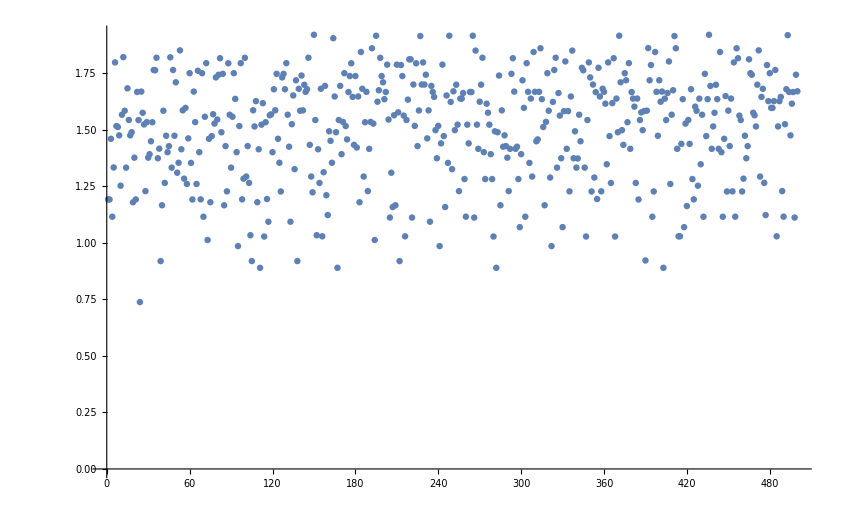

```mathematica
ListPlot[Table[σ3[0.5,0.001,1,0,1],{i,500}]]
```

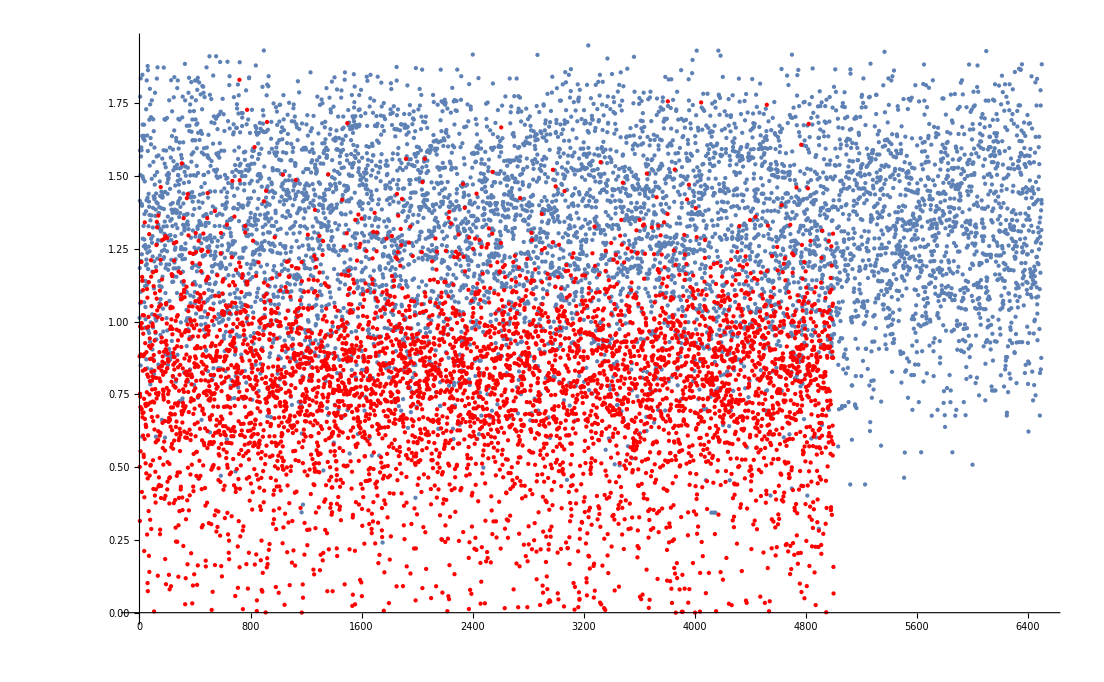

```mathematica
Show[ListPlot[ρ4[0.5,01]],ListPlot[ρ8[0.5,01],PlotStyle->Red]]
```

```mathematica
DeleteDuplicates[%619]
```

{1.90514,1.83991,1.87019,1.94606,1.85144,1.86197,1.94898,1.85662,1.91284,1.91275,1.83991,1.94685,1.96436,1.91275,1.74707,1.92157,1.9061,1.87811,1.99506,1.86197,1.92148,1.82862,1.90361,1.92157,1.91284,1.94606,1.95462,1.90361,1.9061,1.9035,1.94685,1.85144,1.90678,1.90678,1.9035,1.94898,1.82862,1.95462,1.97917,1.97917,1.74707,1.96436,1.95306,1.90514,1.85662,1.87019,1.95306,1.91258,1.97617,1.9595,1.9544,1.82038,1.94299,1.77625,1.9544,1.90981,1.86255,1.98775,1.97617,1.90683,1.90683,1.86355,1.86576,1.90539,1.93974,1.77625,1.92542,1.88393,1.93978,1.88201,1.90672,1.9595,1.89653,1.98775,1.81348,1.86576,1.96534,1.82038,1.88393,1.90539,1.79337,1.91258,1.79337,1.94299,1.86355,1.97869,1.92542,1.93978,1.93974,1.88201,1.90981,1.89653,1.81348,1.97869,1.86255,1.71537,1.85963,1.78323,1.5772,1.81297,1.87893,1.76573,1.7618,1.46395,1.7143,1.91381,1.31605,1.85963,1.79819,1.5772,1.98376,1.7827,1.3844,1.98376,1.87893,1.78323,1.54138,1.7143,1.57675,1.88109,1.54138,1.75623,1.46395,1.88109,1.8085,1.8085,1.31605,1.24345,1.75623,1.24345,1.42578,1.86167,1.7618,1.71537,1.6071,1.3844,1.42578,1.86167,1.79819,1.76573,1.57675,1.81297,1.6071,1.91381,1.86318,1.98927,1.90772,1.90822,1.88541,1.96939,1.82404,1.89947,1.7297,1.90902,1.89871,1.83874,1.8747,1.9547,1.9592,1.90772,1.8747,1.90822,1.8284,1.86318,1.9886,1.89294,1.96128,1.9886,1.8284,1.7361,1.95832,1.95698,1.96939,1.82404,1.95698,1.89871,1.9592,1.7297,1.92085,1.83874,1.89416,1.9547,1.90902,1.7361,1.90543,1.89947,1.95832,1.88541,1.90543,1.89294,1.92085,1.89416,1.96128,1.90687,1.87324,1.87506,1.96859,1.89975,1.81274,1.94194,1.87506,1.96962,1.98397,1.8097,1.97339,1.96859,1.96962,1.89805,1.88242,1.87171,1.87173,1.93361,1.86978,1.94648,1.85775,1.70508,1.87171,1.94648,1.93728,1.90974,1.87601,1.85775,1.87173,1.89805,1.97339,1.89975,1.93728,1.81542,1.8097,1.81542,1.94194,1.93361,1.98397,1.87601,1.86978,1.70508,1.90687,1.81274,1.90974,1.88242,1.92893,1.87324,1.82998,1.7649,1.87793,1.89724,1.88858,1.90142,1.8869,1.92596,1.80836,1.96325,1.9289,1.96628,1.85362,1.9289,1.95926,1.90124,1.87699,1.92503,1.92596,1.96628,1.80558,1.9227,1.9633,1.92503,1.7649,1.86056,1.9227,1.86056,1.91955,1.90142,1.74387,1.80836,1.8869,1.9633,1.96824,1.88858,1.85362,1.95926,1.90124,1.87699,1.80558,1.90117,1.96824,1.74387,1.82998,1.91955,1.87793,1.90117,1.74521,1.88311,1.9609,1.94125,1.90279,1.90933,1.87863,1.77998,1.83572,1.96136,1.88445,1.90933,1.88415,1.74403,1.91165,1.91321,1.85887,1.93918,1.96136,1.90279,1.90638,1.99972,1.97482,1.83603,1.9579,1.85887,1.90735,1.88415,1.94125,1.9609,1.74403,1.91321,1.76894,1.83603,1.77998,1.74521,1.91165,1.83572,1.9579,1.95683,1.95683,1.87863,1.76894,1.90735,1.93918,1.88311}

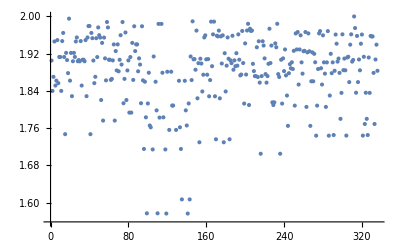

```mathematica
ListPlot[%624]
```

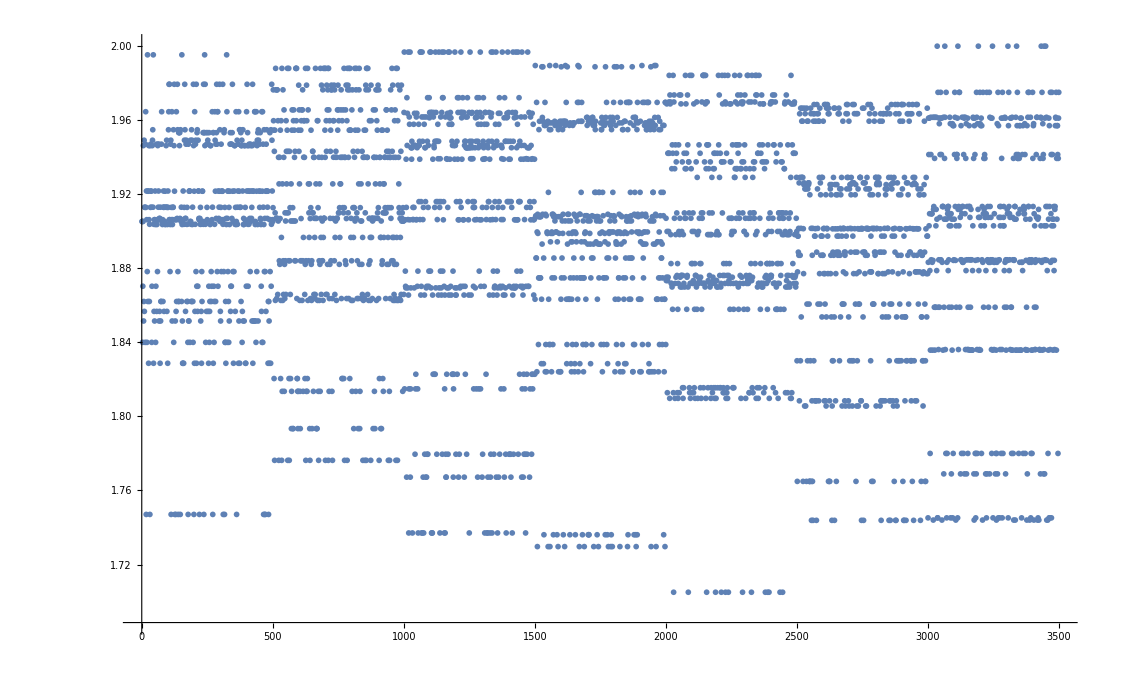

```mathematica
ListPlot[ρ2[0.5,0.5]]
```

```mathematica
Interpolation[%619]
```

InterpolatingFunction[…]

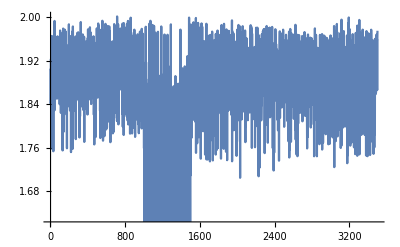

```mathematica
Plot[%622[x],{x,1.,3500.}]
```

```mathematica
DistributionFitTest[%619,Automatic,"HypothesisTestData"]["TestDataTable",All]
```

General::munfl: Exp[-2027.19] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1727.99] is too small to represent as a normalized machine number; precision may be lost.

| Statistic | P-Value
Anderson-Darling | 220.698 | 0.
Baringhaus-Henze | 242.559 | 0.
Cramér-von Mises | 37.2262 | 0.
Jarque-Bera ALM | 15215.7 | 0.
Mardia Combined | 15215.7 | 0.
Mardia Kurtosis | 105.403 | 0.
Mardia Skewness | 4046.77 | 0.
Pearson χ^2 | 3818.6 | 0.
Shapiro-Wilk | 0.739066 | 2.94707×10^-59

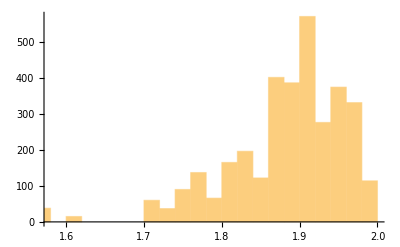

```mathematica
Histogram[%619]
```

```mathematica
For[i=0.1,i<3,i+= 0.2,Print[λ[i,0.5]];Print[i]]
```

```mathematica
ρ8[0.5,0.5]
```

{1.54479,1.67161,1.41928,0.695387,0.99795,1.17932,1.58783,1.6918,1.34028,1.71888,1.77433,1.28481,1.33341,1.60285,1.63677,1.46061,1.31704,1.43638,1.45022,1.54456,1.46998,1.27529,1.56316,1.5354,1.43836,1.48568,1.56462,1.56008,1.03956,1.64859,1.44021,1.46662,1.4822,1.51246,1.54661,1.34378,1.36104,1.67304,1.16905,1.39704,1.27832,1.37031,1.71174,1.77822,1.37009,1.65922,1.37814,1.13984,1.63646,1.68377,1.1322,1.32483,1.17702,1.13354,1.24135,1.46639,1.30309,1.3089,1.29367,1.50224,1.30145,1.53351,1.42363,1.63791,1.30264,1.42073,1.3662,1.54012,1.31602,1.48921,1.50393,1.68808,1.66531,1.15528,1.51,0.822521,1.3291,1.39409,1.73303,1.29577,1.29917,1.34025,1.35166,1.68183,1.35177,1.25851,1.20704,1.3855,1.10727,1.73355,1.04959,1.63815,1.50039,1.08289,1.11646,1.06798,1.81904,1.80383,1.31416,1.58313,1.41324,1.23864,1.65739,1.2646,1.67292,1.63222,1.50242,1.26969,1.23635,1.59353,1.60082,1.3389,1.70125,1.56533,1.48719,1.22961,1.5957,1.39019,1.39157,1.62913,1.63581,1.08433,1.28801,1.64397,1.57013,1.62849,1.49762,1.32292,1.32226,1.59476,1.60418,1.58123,1.5711,1.55691,1.19189,1.05452,1.66415,1.47853,1.1252,1.34599,1.24564,1.60966,1.29739,1.28572,1.5555,1.43885,1.64914,1.10535,1.54564,1.54473,1.57087,1.50741,1.23977,0.876792,1.22224,1.35815,1.67231,1.38223,1.48406,1.42617,1.11897,1.4943,1.00972,1.19642,1.68962,1.65324,1.09359,1.464,1.48865,1.35538,1.4084,1.10934,1.33494,1.63444,1.29885,1.16058,1.5225,1.25188,1.59923,1.33436,1.50725,1.39359,1.60974,1.44216,0.916823,1.67509,1.54796,1.53359,0.989483,1.52896,1.49294,1.43976,1.68156,1.60274,1.32646,1.54011,1.7824,1.35432,1.55702,1.73976,1.56726,1.3623,1.42832,1.67973,1.02581,1.61836,1.49039,1.46225,1.66153,1.46663,1.32463,1.39791,1.0679,1.40502,1.50533,1.31525,1.47894,1.22387,1.60982,1.08603,1.77166,1.28983,1.19047,1.33669,1.68179,1.10548,1.59203,1.52625,1.54617,1.66354,1.05997,1.58674,1.61981,1.10852,1.61857,1.51549,1.24002,1.54029,1.44064,1.24237,1.36997,1.17436,1.23365,1.46599,1.305,1.4787,1.27777,1.61297,1.65381,1.67944,1.01451,1.65088,1.49386,1.18963,1.35312,1.42248,1.5383,1.20788,0.889939,1.53702,1.55258,1.3795,1.75984,1.28923,1.19922,1.53966,1.30731,1.09779,1.13264,1.48258,1.33268,1.37966,1.83777,1.36198,1.61747,1.41682,1.59601,1.73486,1.64932,1.41475,1.35127,1.5508,1.2481,1.23333,1.25988,1.67602,1.38488,1.69807,1.543,1.77593,1.55151,1.1043,1.61345,1.34835,1.45535,1.0462,1.57005,1.38262,1.49597,1.5528,1.4739,1.54349,1.28911,1.44389,1.45493,1.32312,1.39808,1.40434,1.37936,1.26268,0.959062,1.82676,1.34551,1.20584,1.48059,1.54104,1.57062,1.4562,1.68862,1.37079,1.63576,1.54958,1.09117,1.65338,1.56328,1.05324,1.39131,1.22089,1.66821,1.16561,1.20751,1.47033,1.5267,1.24182,1.43905,1.57378,1.65939,1.66806,0.970483,1.49564,1.28033,1.63164,1.71406,1.22342,1.27283,1.72931,1.54804,1.78769,0.809008,1.37241,1.46566,1.37832,1.66748,1.70278,1.38479,1.28119,1.58094,1.6948,1.2461,1.55074,1.22005,1.24136,1.19041,1.4469,1.25707,1.51353,1.26637,1.54143,1.62909,1.22259,1.63157,1.23946,1.3762,1.45002,1.48596,1.58093,1.19456,1.58907,1.45245,0.932892,1.10098,1.71892,1.63318,1.38955,1.51356,1.80784,1.45059,1.28174,1.55548,1.41987,1.56801,1.64003,1.48095,0.869647,1.74069,1.09113,1.56965,1.29832,1.50516,1.66581,1.72778,1.50591,1.37067,1.25733,1.27708,1.60618,1.29094,1.32951,1.68157,1.40282,1.5152,1.66226,1.49349,1.46453,1.62015,1.44235,1.50771,1.0889,1.54268,1.6416,1.4466,1.54361,1.56038,1.36272,1.5204,1.46828,1.56846,1.5939,1.70237,1.52933,1.72064,1.30904,1.72622,1.76594,1.27962,1.52075,1.78922,1.19686,1.29752,1.18622,1.26388,1.3362,1.43727,1.35234,1.39299,1.35222,1.229,1.39754,1.39276,1.76354,1.46168,1.50665,0.999606,1.0653,1.58366,1.51389,1.7503,1.06474,1.2198,1.42061,1.63142,1.37614,1.40168,1.65888,1.1432,1.24943,1.2139,1.48156,1.36498,1.60659,1.4147,1.3097,1.49701,1.479,1.10186,1.57395,1.44898,1.40214,1.49123,1.42239,1.22126,1.54577,1.71216,1.42509,1.754,1.6166,1.6605,1.4664,1.54009,1.75724,1.35698,1.64623,1.56875,1.17857,1.54127,1.28409,1.19255,1.40547,1.46829,1.44742,1.29709,1.12719,1.48502,1.42079,1.55026,0.956854,1.45482,1.18074,1.43343,1.14153,1.47218,1.63285,1.16077,1.53786,1.24657,1.40915,1.75646,1.42657,1.35547,1.30173,1.30913,1.49538,1.08674,1.45468,1.62508,1.4676,1.62589,1.18771,1.68886,1.32351,1.43667,1.44074,1.75539,1.15103,1.48121,0.945312,1.49848,1.79783,1.32068,1.50138,1.52589,1.55439,1.19263,0.793031,1.41209,1.53064,1.40189,1.54023,1.40059,1.56799,1.49273,1.51098,1.36964,0.937425,1.52578,1.52426,1.22512,1.13708,1.51975,1.42041,1.32782,1.28349,1.07295,1.20466,1.33062,1.53832,1.46238,1.49693,1.52626,1.15021,1.07829,1.30509,1.52458,1.25104,1.56742,1.38459,1.30337,1.76581,1.19529,0.960622,1.51137,1.24787,1.37234,1.61499,1.51053,1.47067,1.16673,1.6211,1.03647,1.59796,1.63193,1.37136,1.32431,1.29399,1.75253,1.36512,1.43213,1.56437,1.1863,1.69131,1.48974,1.56563,1.67426,1.68287,1.32956,1.17593,1.59242,0.790604,1.39664,1.56532,1.7743,0.917818,1.67405,1.28627,0.806982,1.43411,1.28916,0.917745,1.55324,1.61233,1.74234,1.71676,1.52723,1.65,1.72007,1.43589,1.68273,1.35005,1.45258,1.57243,1.69565,1.40159,1.68999,1.12045,1.24987,1.38017,1.47545,1.32605,1.35505,1.37707,1.64354,1.62009,1.48062,1.31684,1.52083,1.43446,1.84422,1.43438,1.72898,1.14909,1.30166,1.61596,1.24014,1.22442,1.56575,1.63753,1.42107,1.6735,1.5007,1.60734,1.71357,1.0471,1.52844,1.48557,1.50351,1.27495,1.45668,1.35635,1.22889,1.13752,0.955068,1.55525,1.52863,1.0403,1.53178,1.30229,1.44918,1.32899,1.08681,1.48702,1.3773,1.34472,1.17801,1.34132,1.1689,1.0782,1.71541,1.12657,1.33934,1.38577,1.30334,1.3462,1.04524,1.62556,1.27211,1.53442,1.2175,1.50633,1.42132,1.48819,1.09538,1.43286,1.62919,1.46348,1.40029,1.74858,1.14288,1.6871,1.31707,1.65483,1.26128,1.51996,1.46012,1.06029,1.91034,1.5362,1.5031,1.17843,1.39974,1.31473,1.4618,1.54852,1.27136,1.49908,1.34045,1.4263,1.47365,1.60186,1.40887,1.49115,1.39177,1.59946,1.2415,1.20653,1.51981,1.26119,1.21613,1.40406,1.22297,1.26548,1.25498,1.39801,1.53755,1.35762,1.41619,1.53823,1.49762,1.34115,1.44141,1.53208,1.44208,1.58712,1.44313,1.38026,1.26521,1.27703,1.58366,1.51917,1.5981,1.61942,1.67398,1.33474,1.45231,1.27568,0.730851,1.35961,1.25977,1.74699,1.47462,1.09409,1.28294,1.40533,1.49136,1.01482,1.28965,1.49737,1.58851,1.4035,1.44509,1.36051,1.31693,1.38993,1.44928,1.30772,0.676391,1.53641,1.51405,1.51868,1.67701,1.36656,1.53203,1.35372,1.33394,1.10949,1.44818,1.04498,1.52712,1.56243,1.32583,1.37185,1.53411,1.39927,1.62349,1.73917,1.08965,1.39324,1.4095,1.26726,1.59548,1.54949,1.69842,1.29412,1.71245,1.19056,1.4238,1.2593,1.57685,0.904898,1.44656,1.41016,1.57344,1.68626,1.87337,1.56277,1.18467,1.46701,1.57644,1.27998,1.4725,1.1427,1.24084,1.55004,1.60982,1.30625,1.56386,1.62745,1.1472,1.4179,1.47344,1.37583,1.24687,1.40608,0.805391,1.12287,1.79934,1.08802,1.3109,1.54683,1.4635,1.76247,1.27128,1.18365,1.28415,1.53208,1.49324,1.40337,1.43987,1.29907,1.64132,1.5119,1.37032,1.44378,1.50315,1.6894,1.24915,1.21785,1.32356,1.27952,1.37134,1.31292,1.70481,1.47054,1.55016,1.43192,1.71206,1.67112,1.28441,1.39482,1.56432,1.41982,1.56463,1.11564,1.84489,1.62044,1.41156,1.31288,1.41066,1.64227,1.32924,1.61156,1.52941,1.38356,1.73248,1.48466,1.15789,1.59453,1.60599,1.29803,1.64614,1.60019,1.16062,1.63254,1.44859,1.70437,1.72006,1.43942,1.38694,1.65947,1.53541,1.37832,1.66655,1.50987,1.64673,1.71044,1.35245,1.63644,1.00909,1.42022,1.34549,1.32687,1.34144,1.59329,1.43584,1.53298,1.5559,1.48236,1.18903,1.50073,1.67522,1.49752,1.45804,1.21725,1.56988,1.40228,1.44652,1.26133,1.12659,1.33372,1.25464,1.21224,1.73646,1.4533,1.34275,1.25571,1.27906,1.73042,1.34423,1.53182,1.63253,1.16786,1.52876,1.57898,1.74059,1.07762,1.2086,1.5865,1.74625,1.47329,1.49287,1.39347,1.57462,1.69385,1.44629,1.62132,1.4109,0.945738,1.04717,1.42474,1.18032,1.1639,1.4299,1.27715,1.78443,1.18897,1.44029,1.47802,1.40096,1.66338,1.45526,1.49584,1.66308,1.39192,1.57246,1.24835,1.49633,1.43654,1.37957,1.51489,0.647079,1.19049,1.59989,1.17101,1.4277,1.5153,1.59076,1.54025,1.32442,1.36346,1.37584,1.19091,1.38109,1.27019,1.26726,1.68002,1.57427,1.1827,1.29218,1.31615,1.42333,1.47637,1.57736,1.10514,1.25892,1.38155,1.30422,1.16617,1.31746,0.990254,1.24579,1.51082,1.55882,1.44151,1.22956,1.33277,1.17625,1.25982,1.29749,1.66555,1.67606,1.27375,1.87753,1.16218,0.970055,0.999556,1.38978,1.39322,1.17086,1.35067,1.50706,0.940968,1.47562,1.25664,1.46643,1.70735,1.24945,1.59965,1.50121,1.47537,1.58899,1.50901,1.43024,1.00258,1.32557,1.56985,1.50917,1.42576,1.75799,1.63423,1.59044,1.38842,1.32153,1.02669,1.16904,1.5316,1.29049,1.29811,1.21912,1.27175,1.50286,1.17594,1.25633,1.41088,1.61546,1.42729,1.24772,1.20627,1.62084,1.39912,1.40054,1.54329,1.213,1.41445,1.35748,1.33787,1.34109,1.40018,1.25942,1.28043,1.45785,1.24985,1.4495,1.46897,1.43283,1.53062,1.41215,1.57027,1.35087,1.36978,1.60751,1.66552,1.55555,1.64609,1.28957,0.906455,1.63761,1.51161,1.5413,1.41789,1.52955,1.20448,0.93464,1.23058,1.17271,1.54789,1.14084,1.02884,1.21247,1.31593,1.56327,1.21314,1.7834,1.45954,1.601,1.49006,1.36715,1.52368,1.11788,1.48975,1.43647,1.18217,1.23899,1.57731,1.63364,1.38053,1.3879,1.48571,1.22698,1.5176,1.12537,1.29526,0.903605,1.48936,1.46799,1.35453,1.4689,1.09269,1.43463,1.56324,1.10636,1.15823,1.47527,1.23349,1.6379,1.18883,1.44029,1.08655,1.32814,1.49055,1.29919,1.49335,1.47643,1.74363,1.72857,1.54405,1.35361,1.62592,1.24777,1.46608,1.35608,1.41161,1.22648,1.59433,1.49519,1.38168,0.870747,1.63599,0.980608,1.68513,1.59172,1.82901,1.08791,1.35647,1.34721,1.64458,1.63374,1.46665,1.3962,1.50571,1.10616,1.4278,1.57714,1.42526,1.29675,1.34741,1.74879,1.49638,1.49233,1.41602,0.720788,1.48057,1.48192,1.41443,1.59729,1.06154,1.19865,0.987736,1.60436,1.05506,1.02338,1.42402,1.48501,1.1067,1.23898,1.48083,1.68207,1.33749,1.60255,1.46615,1.622,1.80981,1.52398,1.57833,1.52179,1.43482,1.19802,1.71649,1.53978,1.49175,1.67439,1.50633,1.14753,1.28785,1.48211,1.71564,1.7136,1.67309,1.41171,1.5331,1.53837,1.49203,0.957035,1.16973,1.23916,1.3593,1.47974,1.13984,1.12265,1.0247,1.42699,1.35127,1.63608,1.0426,1.66161,1.55953,1.44847,1.54308,1.37478,1.29693,1.43994,1.54882,1.15833,1.29709,1.51106,1.70086,1.36168,1.64669,1.19391,1.22112,1.55643,1.10711,1.82162,1.06077,1.69339,1.51266,1.47879,1.34321,1.11512,1.26167,1.75237,1.5365,1.24109,1.30559,1.18949,1.43891,1.24895,1.44598,1.61479,1.49709,1.72728,1.43409,1.50112,1.41599,1.42413,0.970646,1.64837,1.62247,1.54892,0.805975,1.55905,1.29042,1.48517,1.37085,1.26316,1.50159,1.44533,1.49117,1.67005,1.75857,1.30955,1.20164,1.35269,1.44195,1.52114,1.3355,1.41066,1.12156,1.53196,1.73588,1.38204,1.30328,1.49015,1.24816,1.25631,1.47704,1.59799,1.69949,1.43734,1.70539,1.44621,1.50874,1.05297,1.06947,1.0912,1.62168,1.353,1.30277,1.41244,1.56976,1.26497,1.4143,1.36524,1.05303,1.52068,1.61001,1.02525,1.52953,1.36502,1.6753,1.33228,1.57385,1.46258,1.80705,1.62937,1.22712,1.49084,1.40837,1.37571,1.19206,1.12324,1.35881,1.51464,1.40351,1.41232,1.57232,1.15991,1.36302,1.41259,1.49461,1.475,1.44274,1.19033,1.55246,1.27989,1.30151,1.27234,1.5529,1.35543,1.44244,1.32955,0.664167,1.39495,1.33551,1.39032,1.54832,1.70621,1.18393,1.51022,1.60595,1.45351,0.895859,1.22556,1.4454,1.33443,1.5064,1.17163,0.793856,1.54728,1.51473,1.35237,1.06069,1.75557,1.25366,1.38946,1.65334,1.47061,1.13533,1.62605,1.11908,1.46823,1.18413,1.36128,1.66171,1.47229,1.25996,1.14128,1.14734,1.40905,1.48341,1.11687,1.12455,1.60602,1.7394,1.72154,1.00142,0.96357,1.45624,1.18366,1.31017,1.20682,1.11478,1.57161,1.56098,1.79043,1.32531,1.38984,1.48577,1.78357,1.36594,1.40955,1.68058,1.26265,1.10684,1.7855,1.64283,1.56909,1.6512,1.42606,1.49128,1.34702,0.937388,1.79529,1.57549,1.75463,1.35856,1.38335,1.40482,1.22001,1.53367,1.26625,1.12334,1.53931,1.633,1.46942,1.18129,1.37832,1.49163,1.64698,1.16963,1.36415,1.64328,1.44233,1.47371,1.51036,1.60021,1.27357,1.68552,1.27407,1.64895,1.09185,1.07107,1.34877,1.51083,1.27351,1.63784,1.43437,1.31992,1.51366,1.23166,1.27388,1.23341,1.59502,1.19325,1.12087,1.52204,1.75217,1.11344,1.33426,1.71004,1.28213,1.43953,1.25785,1.64691,1.32002,1.61528,1.27942,1.48434,1.28431,1.37173,1.23638,1.61511,1.48888,1.63045,1.75894,1.23402,1.17761,1.17587,1.05457,1.29032,1.43308,1.36332,1.32012,1.40824,1.62015,1.53966,1.52606,1.39779,1.49904,1.36893,1.57747,1.44594,1.35815,1.27362,1.30578,1.57215,1.40007,1.25422,1.5092,0.951416,1.25101,1.13187,1.3405,0.930276,1.65707,1.66703,1.68727,1.50274,1.33648,1.03897,1.62555,1.25632,1.00663,1.59337,1.36555,1.33474,1.46451,1.49285,1.41764,1.38661,1.35219,1.37903,0.87188,1.53937,1.64081,1.51655,1.6904,1.33842,1.33883,1.08331,1.42454,1.15378,1.54365,1.4446,1.42557,1.03702,1.29817,1.1396,1.55125,1.54506,1.3362,1.11685,1.25638,1.34796,0.821016,1.64801,1.00572,1.72423,1.48725,1.45591,1.45134,1.58352,1.2795,0.462379,1.40863,1.51237,1.18128,1.3723,1.61767,1.21509,1.69101,1.66866,1.71245,1.1774,1.76308,1.38296,1.52831,1.67459,1.35975,1.54817,1.49982,1.38062,1.58521,1.42534,1.47539,1.37481,1.3761,1.64974,1.2243,1.6528,1.14778,1.45332,1.44008,1.36696,1.20453,1.49432,1.25413,1.83815,1.41455,1.28412,1.6333,1.36844,1.05951,1.35739,1.77503,1.32251,1.28957,1.25539,1.50802,1.10611,1.43242,1.54519,1.18783,1.41878,1.36457,1.35068,0.84394,1.46056,1.43043,1.40515,1.71267,1.87471,1.41531,1.68911,1.29855,0.85683,1.22971,1.32722,1.50489,1.60992,1.30196,1.56243,1.28552,1.65162,1.46116,1.40188,1.59319,1.78304,0.921916,1.45734,1.43247,1.49793,1.07959,1.47664,1.06812,1.16263,1.34145,1.58662,1.40952,1.70826,1.41083,1.64164,1.51119,1.23025,1.02377,1.2819,1.39615,1.31837,1.51227,1.42695,1.53038,1.36951,1.34817,1.19071,1.24193,1.05885,1.06904,1.08497,1.56878,1.35659,1.74842,1.72954,1.80088,1.54691,1.33068,1.38332,0.822787,1.16734,1.69396,1.65199,1.62098,1.43942,1.47163,1.43119,1.26628,1.66756,1.60153,1.49145,1.24501,1.44474,1.70348,1.13563,0.799045,1.73372,1.32116,1.47535,1.59564,1.40401,1.5959,1.66692,1.47171,1.36999,1.61587,1.45229,1.25773,1.62908,1.29277,1.32615,1.2229,1.64207,1.25696,1.55136,1.18282,1.44383,0.989933,1.61962,1.20666,1.67512,1.60101,1.18192,1.59706,1.54837,1.14249,1.06153,1.64467,1.83325,1.6449,1.35616,1.69153,1.46602,1.62861,0.845209,1.04259,1.2494,1.64238,1.30542,1.50831,1.48182,1.31757,1.76561,1.49993,1.1616,1.66161,1.30268,1.33227,1.2729,1.18346,1.57108,1.14997,1.54675,1.2568,1.10883,1.50676,1.11752,0.833972,1.06082,1.37308,1.43539,1.36093,1.20433,0.898476,1.41318,1.67812,1.61736,1.62829,1.66673,1.21496,1.31429,1.83465,1.66067,1.18397,1.5688,1.69587,1.37151,1.55152,1.23346,1.63259,1.21202,1.49738,1.52853,1.32877,1.26375,1.57958,1.53288,1.17105,1.49356,1.45157,1.56325,1.4062,1.57321,1.38438,1.65747,1.38318,1.2812,1.38066,1.45988,1.51692,1.25971,1.59655,1.54704,1.474,1.41949,1.7016,1.42503,1.5478,1.16224,1.55991,1.57639,1.48058,1.28248,1.15177,1.3027,1.28945,1.30768,1.23509,1.36626,1.01973,1.57377,1.579,1.35962,1.49146,1.41565,1.39006,1.41199,1.35317,1.47683,0.815716,1.55105,1.38977,0.991583,1.52576,1.40008,1.69242,1.55145,1.43425,1.76159,1.21766,1.45511,1.30004,1.35379,1.57548,1.39134,1.40977,1.34804,1.23819,1.77198,1.65937,1.09276,1.63995,1.25412,1.59519,1.65582,1.81433,1.49619,1.56999,1.44333,1.18,1.54401,1.25764,1.72376,1.3147,1.35883,1.27353,1.5621,1.63218,1.18794,1.64278,1.55031,1.40344,1.40478,1.33196,1.4486,1.5654,1.2242,1.00296,1.66596,1.6481,1.57024,1.49339,1.37872,1.51793,1.46339,1.39998,1.37903,1.38321,1.52272,1.23681,1.40613,1.25454,1.5956,1.1648,1.2759,1.08619,1.42379,1.44731,1.16467,1.45809,1.45547,1.41306,1.69085,1.39385,1.5059,1.4811,1.41175,1.45891,1.48954,1.34388,1.33424,0.906553,1.41162,1.30596,1.42072,1.52124,1.38589,1.15644,1.32375,1.09103,1.05679,1.61328,1.46863,1.55914,1.87957,1.5511,1.49633,1.63853,1.45022,1.47497,0.833807,1.33558,1.3373,1.68521,0.958904,1.57332,1.37771,1.79911,1.48847,1.21974,1.46205,1.51731,1.61456,1.5992,1.1679,1.37792,1.36409,1.37106,1.31778,1.68511,1.75885,1.4509,1.45804,1.02872,1.31444,1.4065,1.04873,1.29013,1.45257,1.59575,1.21333,1.4757,1.29695,1.57399,1.59221,1.46824,1.36059,1.19723,1.42598,1.3398,1.08552,1.25332,1.4116,1.66412,0.802313,1.64593,1.36785,1.4555,1.5989,1.69137,1.65538,1.52425,1.40716,1.46633,1.02817,1.52778,1.68585,1.605,1.12944,1.3423,1.77192,1.34242,0.904364,1.60875,1.80513,1.67727,1.30502,1.40847,1.76343,1.12698,1.53286,1.27615,1.28014,1.68263,1.60995,1.58429,1.41569,1.22059,1.50408,1.34256,1.43654,1.52504,1.68115,1.53446,1.42104,1.25763,1.43815,1.19096,1.6144,1.64544,1.45438,1.68804,1.72735,1.30245,1.19272,1.63716,0.990658,1.57546,1.62643,1.35878,0.899364,1.19332,1.29623,0.949416,1.60147,1.62205,1.08043,1.29224,1.48043,1.59918,1.2355,1.58389,1.4989,1.38324,1.10063,1.61668,1.33491,1.31157,1.58665,1.25182,1.34127,1.41675,1.52505,1.35014,1.14908,1.39358,1.21819,1.35033,1.59341,1.45831,1.67005,1.62388,1.51895,1.40607,1.4034,1.1446,1.01238,1.50029,1.13977,1.52811,1.42237,1.06717,1.19466,1.56125,1.12435,1.58046,1.83599,1.63975,1.75381,1.43749,1.3788,1.1284,1.35269,1.32834,1.28264,1.26043,1.53145,1.58336,1.2788,1.39489,1.25527,1.29006,1.27651,1.40915,1.48642,1.55162,1.25519,1.37636,1.38256,1.15812,1.37774,1.60647,1.42035,1.34145,1.28845,1.57162,1.77964,1.4759,1.70657,1.62273,1.44547,1.59746,1.45938,1.59269,1.54609,1.62946,1.41396,1.51424,1.14856,1.54425,1.63205,1.45922,1.29152,1.32087,1.38282,1.42925,1.48826,1.67447,1.08365,1.03407,1.68183,1.19148,1.79718,1.28707,1.4493,1.13067,1.19783,1.23116,1.35694,1.62306,1.19483,1.53794,1.37383,1.55652,1.68043,1.06333,1.35395,1.60632,1.25307,1.61583,1.61616,1.21335,1.44215,1.19906,1.15388,1.24427,1.19293,1.35041,1.4217,1.54894,1.42844,1.49295,1.51504,1.72882,1.4422,1.29103,1.56016,1.65757,1.20895,1.18797,1.3946,1.45825,1.52154,1.11773,1.2938,1.31815,1.35285,1.37978,1.73658,1.44925,1.11669,1.34339,1.41324,1.27913,1.62617,1.18064,1.52009,1.69636,1.67124,1.11955,1.44248,1.51364,1.25969,1.59112,1.63052,1.56778,0.754591,1.42344,1.63932,1.52146,1.69996,1.43563,1.63508,1.57815,1.61021,1.24609,1.65439,1.66449,1.56363,1.27029,1.79686,1.40771,1.6889,0.890611,1.54522,1.47258,1.43667,1.42804,1.09997,1.65051,1.50491,1.62835,1.49109,1.6632,1.55704,1.58996,1.61887,1.282,1.52369,1.31004,1.38381,1.37132,0.944064,1.23465,1.51424,1.3124,1.47857,1.41589,1.22708,1.36401,1.29962,1.4155,1.54334,1.42204,1.58335,1.61311,1.3612,1.36189,1.43305,1.22291,1.11757,1.68884,1.34762,1.2447,1.3896,1.32909,1.54249,1.34577,1.69355,1.62685,1.40682,1.41911,1.11244,1.63727,1.22404,1.68552,1.56294,1.2779,1.55661,1.61369,1.70589,1.59811,1.57424,1.57887,1.55561,1.43588,1.43891,1.59398,1.43122,1.19725,1.27123,1.53461,1.26991,1.46401,1.40617,1.04166,1.41156,1.21689,1.62547,1.39408,1.18945,1.23867,1.58131,1.53731,1.27217,1.70685,1.49076,1.70009,1.55712,1.14601,1.49871,1.4387,1.67616,1.22225,1.39079,1.48405,1.62576,1.56304,1.47066,1.32155,1.49044,1.69589,1.52826,1.70518,1.41184,1.36715,1.67975,1.5282,1.82773,1.24658,0.842907,1.12911,1.37007,1.55779,1.45649,1.42529,1.38777,1.31349,1.47322,1.70517,0.970291,1.43373,1.04786,1.55755,1.45666,1.55768,1.64217,1.23963,1.42677,1.18823,1.42843,1.12484,1.57303,1.37275,1.16406,1.25005,1.58911,1.28898,1.70705,1.58947,1.37218,1.34788,1.51554,1.47399,1.50821,1.55508,1.17724,1.3829,1.65142,1.43373,1.22421,1.43568,1.49956,1.50883,1.16993,1.64591,1.3805,1.56838,1.61726,1.61116,1.24615,1.34342,1.58369,1.12522,1.68129,1.59307,1.40154,1.28437,1.38994,1.29929,1.40347,1.67171,1.23179,1.33836,1.37532,1.30142,1.48696,1.54591,1.06101,1.31234,1.24552,1.28006,1.27978,1.35989,1.53836,1.41927,1.12284,1.26901,1.76252,1.45251,1.23619,1.25028,0.924544,1.51208,1.32559,1.50283,1.534,1.39363,1.37449,0.893342,1.77786,1.42543,1.52015,1.30299,1.41785,1.81124,1.6692,1.50552,1.59751,1.45753,1.48072,1.52063,1.66879,0.974622,1.46027,1.24126,1.26711,1.50376,1.37541,1.40405,1.59862,1.38722,1.44894,1.69016,1.5413,1.58346,1.5253,1.16211,1.29579,1.36198,1.37709,1.58206,0.854267,1.68508,1.77145,1.57671,1.40186,1.32124,1.39664,1.48612,1.04162,1.34828,1.45044,1.58176,1.66497,1.11145,1.53996,1.46702,0.823468,1.73192,1.35128,1.45175,1.36238,1.39695,1.47104,1.28246,1.62606,1.22574,1.26077,1.38796,1.4042,1.24298,1.34507,1.26526,1.48816,1.25681,1.06201,1.73372,1.01723,1.29953,1.46662,1.5743,1.4161,1.31779,0.866431,1.54606,1.55467,1.65606,1.62112,1.76056,1.56666,1.66632,1.53361,1.51736,1.5516,1.47467,1.42979,1.71842,1.59329,1.21959,1.33894,1.05149,1.54541,1.28677,1.57743,1.61189,1.52443,1.36102,1.40592,1.71988,1.2519,1.62574,1.18509,1.60311,0.565836,1.51898,1.47573,1.67634,1.68061,1.36647,1.12192,1.49071,1.48683,1.06966,1.20507,1.36333,1.59002,1.19025,1.61216,1.15669,1.27674,1.30661,1.27572,1.22658,1.54495,1.58502,1.5988,1.59572,1.34677,1.64419,1.37423,1.59591,1.5238,1.32521,1.43072,1.55079,1.55425,1.50595,1.30563,1.15196,1.55803,1.65653,1.4416,0.968669,1.25408,1.46949,0.975179,1.60559,1.23708,1.35411,1.40001,1.33779,1.42701,1.21854,1.49365,1.49865,1.73857,1.22859,1.2319,1.69429,1.62814,1.31865,1.25483,1.52331,1.16088,1.31067,1.7733,1.50403,1.49613,1.36556,0.985051,1.13284,1.17855,1.31153,1.5028,1.38839,1.53033,1.51126,1.4003,1.42059,1.14633,1.55996,1.61395,1.47923,1.41291,1.07095,1.6448,1.50208,1.04311,1.34291,1.6349,1.38073,1.67744,1.32687,1.59601,1.37723,1.35295,1.4975,1.63505,1.39724,1.24372,1.45985,1.58347,1.45122,1.32638,1.42708,1.50356,1.45588,1.67124,1.381,1.37193,1.3543,1.47159,1.0128,1.44019,1.39615,1.2013,1.43494,1.62295,1.48993,1.00311,1.07791,1.31049,1.49878,1.32249,1.61378,1.72572,1.52984,1.09898,1.41447,1.71901,1.36123,1.35833,1.68253,1.3498,1.61637,1.46154,1.03502,1.33157,1.65634,1.61365,1.5078,1.03594,1.24984,0.97419,1.45966,1.02164,1.46605,1.30716,0.955673,1.41254,1.25483,1.45598,1.4267,1.52243,1.35635,1.6611,0.900754,0.862901,1.34748,1.59741,1.44134,1.7498,1.45743,1.07446,1.22981,1.49271,1.41426,1.35368,1.71333,1.38103,1.53229,1.42499,1.43889,1.51271,1.23858,1.39804,1.58501,1.49264,1.1977,1.24147,1.45633,1.48552,0.667562,1.76474,1.64618,1.61151,1.24538,1.39553,1.44373,1.07137,1.53552,1.64073,0.997611,1.06338,1.76782,1.40211,1.23409,1.85368,1.69935,1.0419,1.58628,1.4918,1.4312,1.14751,1.50817,1.49702,1.29478,1.31831,1.50045,1.64839,1.60724,1.62554,1.35514,1.39134,1.37112,1.49749,1.64371,1.64109,1.26079,1.37274,1.41263,1.53193,1.53574,1.28121,1.61458,1.47972,1.55889,1.31537,1.5161,1.52226,1.91223,1.34823,1.48485,1.20148,1.6201,0.795216,1.4279,1.13362,1.20508,1.25111,1.3313,1.46819,1.45436,1.66338,1.24546,1.34156,1.01659,1.38513,1.64918,1.03594,1.49754,1.56894,1.61405,1.21849,1.48169,1.33385,0.979431,1.15394,1.19385,1.38654,1.55085,1.18912,1.46836,1.84081,1.21395,1.32763,1.7225,1.4494,1.6494,1.48026,1.83271,1.53806,1.78839,1.28081,1.44243,1.24313,1.77496,1.26563,1.43622,1.46348,1.25807,1.20954,1.33334,1.39268,1.66062,1.72665,1.35507,1.51835,1.62302,1.73238,1.43667,1.09744,1.59314,1.3376,1.40604,1.27455,1.14333,1.15278,1.6682,1.68765,1.37122,1.70594,1.53141,1.44696,1.37136,1.55214,1.70705,1.05478,1.25834,1.55528,1.39643,1.04027,0.963234,1.61715,1.57463,1.36039,1.30832,1.34971,1.53359,1.35059,1.30098,1.46379,1.68395,1.20624,1.32637,1.19788,1.59526,1.33174,1.38565,1.60885,1.09651,1.62506,0.98139,1.38408,1.49063,1.62781,1.26466,1.44834,1.30778,1.42691,1.48273,1.43674,1.7558,1.33787,1.4316,1.40738,1.46398,1.46973,1.41275,1.315,1.4097,1.38139,1.68087,1.48821,1.5707,1.58657,1.4625,1.59893,1.28837,1.46437,1.30762,1.37405,1.33031,1.22206,1.61271,1.34176,1.27647,1.5915,1.61025,1.53279,1.21529,1.33086,1.61274,1.56386,1.5418,1.48973,1.13841,1.3113,1.59452,1.2989,1.37404,1.54289,1.48261,1.61142,1.8209,1.64447,1.55364,1.54184,1.51782,1.39154,1.45639,1.56501,1.23899,1.26372,1.51075,1.3245,1.39311,1.56342,1.48033,1.79394,1.6575,1.28678,1.44992,1.13868,1.58403,1.60969,1.66121,1.55167,1.23127,1.64553,0.8547,1.02916,1.66864,1.5471,1.74807,1.56798,1.44061,1.43569,1.29084,1.75333,1.44464,1.66663,1.77143,1.78454,1.15391,1.39847,1.12717,1.53141,1.32207,1.42137,1.78725,1.60539,1.30702,1.25574,1.52387,1.14983,1.52383,1.21931,1.26347,1.633,1.32054,1.75513,1.55854,1.13655,1.4214,1.34749,1.74716,1.38106,1.46684,1.23937,1.59224,1.71041,1.54109,1.23596,1.09737,1.55362,1.25778,1.57963,1.60964,1.43559,1.48973,1.44305,1.61229,1.59103,1.79507,1.45674,1.27553,1.5084,1.45721,1.08993,1.31107,1.1267,1.45341,1.79869,1.83115,1.39388,1.58892,1.36196,1.56046,1.33372,1.43461,1.27669,1.44359,1.49132,1.72437,1.16523,1.36875,1.54975,1.45942,1.43007,1.66072,1.52748,1.33672,1.49787,1.72168,1.5965,1.20684,1.54612,1.33899,1.15935,1.6458,1.48162,1.57541,1.42672,1.5021,1.57012,1.54546,1.51528,1.67535,1.26002,1.15393,1.51064,1.25515,1.36702,1.41254,1.28142,0.830657,1.32838,1.38181,1.20744,1.59796,1.58459,1.33119,1.39006,1.28669,1.60794,1.51861,0.867782,1.40553,1.74009,1.67676,1.6992,0.977841,1.5324,1.44823,1.2329,1.20627,1.25186,1.32883,1.47587,1.24402,1.48068,1.5743,1.58005,1.01154,1.07404,1.11,1.34118,1.2802,1.24386,1.39643,1.61699,1.71027,1.65246,1.41584,1.49792,1.50301,1.75246,1.43512,1.1485,1.17886,1.50281,1.29609,1.36065,1.27096,1.71984,1.56929,1.18131,1.51989,1.46162,1.4183,1.30535,0.969964,1.32446,1.4324,1.63174,1.52453,1.29415,1.10019,1.64934,1.58571,1.61957,1.6103,1.68365,1.65923,1.13242,1.34209,1.43217,1.40398,1.18016,1.6573,1.30163,1.31811,1.18974,1.45316,1.53154,1.21563,1.31895,1.2986,1.47524,1.17996,1.49302,1.67167,1.60829,1.37295,1.10664,1.57788,1.38851,1.17379,1.73403,1.53789,1.46183,1.04293,1.09386,1.53475,1.49851,1.52977,1.32379,1.38617,1.50138,1.44531,1.25998,1.33283,1.67984,1.37708,1.59688,1.13451,1.22884,1.54712,1.46096,1.42977,1.30211,1.27995,1.71818,1.12738,1.37579,0.588891,1.59574,1.46453,1.49932,1.66004,1.52957,1.54773,1.3274,1.13653,1.35388,1.44877,1.3639,1.63902,0.956211,0.986897,1.32572,1.4252,1.30043,1.25198,1.20289,1.38259,1.18741,1.54667,1.59524,1.59726,1.21186,1.44082,1.37879,1.0142,1.54054,1.50383,1.24748,1.61053,1.70248,1.31155,1.35261,1.51389,1.42659,0.979869,1.21777,1.62856,1.26109,1.49778,1.31462,1.3462,1.47447,1.37104,1.31434,1.30073,1.39381,1.57052,1.65648,0.898361,1.53299,1.04009,1.31369,1.27204,1.57016,1.58231,1.50839,1.03358,1.59267,0.978782,1.2733,1.3572,1.72586,1.42349,1.68413,1.6944,1.60488,1.37223,1.53337,1.42912,1.58517,1.02934,1.04053,1.49566,1.16207,1.41445,1.31966,1.07266,1.4325,1.638,1.37774,1.35582,1.36982,1.63563,1.35613,1.49908,1.22792,1.16302,1.44496,1.65156,1.494,1.28219,1.53604,1.34409,1.3828,1.2232,1.72164,1.66662,1.3196,1.43025,1.59598,1.83607,1.73847,1.59396,1.47438,1.20921,1.43523,1.48999,0.846839,1.16102,1.57654,1.32186,1.73269,1.12062,1.4603,1.58131,1.03851,1.6137,1.6793,1.50478,1.60997,1.60865,1.65155,1.62885,1.51672,1.23934,1.08001,1.54401,1.65683,1.61747,1.51987,1.63471,1.52779,1.17172,1.62758,1.52669,1.54706,1.25939,1.31521,1.39919,1.30286,1.04503,1.32392,1.40945,1.18641,1.4841,1.59168,1.29601,1.37488,1.52678,1.43179,1.46625,1.56328,1.55679,1.19843,1.56455,1.21563,1.63107,1.47583,1.29546,1.68602,1.42387,1.35634,1.31123,1.25655,1.47012,1.53526,1.45423,1.60863,1.02208,1.38498,1.39532,1.31345,1.53577,1.47117,1.4699,1.3808,1.44867,1.46908,1.24451,1.54521,1.40029,1.20896,1.47214,1.20242,1.38387,1.50355,1.25583,1.48572,1.28186,1.14877,1.39129,0.866636,1.11168,1.20781,1.42957,1.45957,1.03061,1.12229,1.10821,1.40265,1.39347,1.57629,1.51847,1.27937,1.59115,1.47699,1.19161,1.44949,1.65421,1.51018,1.41464,1.35414,1.55305,1.49081,1.60316,1.27768,1.56435,1.51085,1.20565,1.33723,1.2564,1.39093,1.11124,1.55317,1.13841,1.00787,1.36235,1.29055,1.08257,1.71303,1.42975,1.24896,1.2751,1.45485,1.01724,1.37533,1.35938,1.67396,1.27583,1.57194,1.41434,0.976359,1.54311,1.73828,1.55872,0.872134,1.52975,1.42898,1.19532,1.32566,1.18693,1.16183,1.3832,1.34836,1.42885,1.26839,1.25714,1.62674,1.35009,0.810865,1.50287,1.446,1.3839,1.44712,1.90014,1.5282,1.13913,1.25561,1.47152,1.18442,1.45467,1.21008,1.69366,1.45105,1.26526,1.29333,1.45595,1.57926,1.11475,1.3017,1.39015,1.31185,1.25679,1.08589,1.67352,1.65914,1.3044,1.46436,1.33775,1.46167,1.15348,1.36983,1.67138,1.40461,1.62485,1.1165,1.86214,0.981881,1.6686,1.31748,1.37058,1.31687,1.49859,1.547,1.43915,1.34711,1.5078,1.54894,1.28052,1.27803,1.43652,1.70959,1.57137,1.56686,1.62752,1.07897,1.54762,1.52952,1.68842,1.63981,1.54843,1.47976,1.54368,1.24465,1.07153,1.71209,1.41992,1.19695,1.59426,1.09985,1.54443,1.22554,1.65506,1.44235,1.37868,1.56488,1.21961,1.25457,1.36596,1.36827,1.42216,0.892763,1.4473,1.56896,1.41685,1.16368,1.49092,1.49423,1.38595,1.32563,1.43629,1.59088,1.73211,1.25401,1.46196,1.13016,1.8129,1.33079,1.28529,1.6886,1.16187,1.48137,1.62858,1.42569,1.30895,1.50932,1.38534,1.04988,1.38932,1.23264,1.69421,1.34526,1.27277,1.46301,1.3785,1.56351,1.75288,1.17566,1.57905,1.44793,1.5482,1.55567,1.37985,1.5697,1.23115,1.3691,1.44136,1.28954,1.04293,1.66591,1.61918,1.52858,1.63875,1.45719,1.07766,1.22976,1.53228,1.54852,1.3185,1.16238,1.64253,1.57874,1.51265,1.42732,1.55615,0.989637,1.57023,1.36434,1.31572,1.10751,1.47951,0.926966,1.64916,1.1076,1.75462,1.56838,1.31772,1.27017,1.11915,1.50861,1.55243,1.55537,1.16791,1.42577,1.4285,1.30924,1.39066,1.66754,1.47526,1.60597,1.47841,1.55204,1.56762,1.30312,1.5467,1.79065,1.17298,1.17063,1.71861,1.31489,1.20581,1.44971,1.24185,1.6836,1.42259,1.62626,1.43843,1.76343,1.49323,1.48278,0.819193,1.40354,1.5848,1.88762,1.51943,1.18922,1.54197,1.58651,1.33907,1.29392,1.4603,1.53365,1.43168,1.30279,1.73116,1.04597,1.47611,1.21135,1.52792,1.31528,1.41,1.89849,1.55782,1.51996,1.09256,1.62169,1.67417,1.28855,1.10302,1.4913,1.31741,1.31249,1.69499,1.3304,1.58909,1.64334,1.05091,1.54991,1.29084,1.3259,1.55228,1.63445,1.43408,1.74571,1.50453,1.34635,0.929417,1.43474,1.83627,1.17323,1.53443,1.43528,1.11989,1.27807,1.33694,1.38608,1.29232,1.29382,1.5562,1.45461,1.37492,1.43592,1.42994,1.31213,1.09467,1.05804,1.36127,0.760169,1.31293,1.27738,1.68654,1.49782,1.44084,1.29098,1.50814,1.66822,1.53713,1.32506,1.15338,1.17161,1.31997,1.18497,1.31389,1.67729,1.61627,1.38599,1.48269,1.32864,0.957926,1.57848,1.5888,1.57792,1.40563,1.22152,1.36306,1.33571,1.22125,1.3407,1.29835,1.28394,1.61678,1.29551,1.39568,1.82126,1.48949,1.49109,1.34164,1.19758,1.33207,1.70017,1.58082,1.55652,1.25227,1.40752,1.34876,1.19344,0.904765,1.22524,1.59551,1.53481,1.49628,1.19504,1.27011,1.86887,1.32838,1.55824,1.82127,1.40652,1.43719,1.55415,1.56893,1.62044,1.62001,1.69705,1.444,1.34072,1.58417,1.55026,1.42803,1.34916,1.72581,1.55158,1.43307,1.5835,1.42154,1.45146,1.3959,1.40463,1.61943,1.67433,1.44741,1.07818,1.46828,1.33975,1.56037,1.50199,1.51196,1.11495,1.68055,1.62589,1.60506,1.29618,1.08849,1.79226,1.61037,1.69072,1.16881,1.40987,1.51554,1.80207,1.37259,1.3561,1.60234,1.3864,1.41244,1.36726,1.19792,1.60601,1.6855,1.46829,1.56513,1.30791,1.10825,1.26868,0.982255,1.2707,1.51708,1.31629,1.35086,1.44352,1.27709,1.4356,1.7219,1.03487,1.25931,1.32281,1.30239,1.48388,1.37247,1.35064,1.41479,1.65931,1.70204,1.49745,1.01249,1.33653,1.2424,1.41073,1.81659,1.53417,1.60429,1.43275,1.85728,1.47872,1.82629,1.50145,1.37024,0.955704,1.5557,1.67511,0.767109,1.75742,1.35328,1.80833,1.28035,1.67888,1.21049,0.985216,1.49004,1.69095,1.62303,1.37341,1.65368,1.73607,1.55032,1.23306,1.30915,1.4962,1.20251,1.08383,1.47131,1.59482,1.72007,1.83915,1.26315,1.54152,1.36851,1.20791,1.34156,1.82954,1.57513,1.60816,1.50533,1.49496,1.47313,1.3944,1.43367,1.47335,1.68637,1.44635,1.42301,1.46461,1.54972,1.58359,1.44861,1.4249,1.33298,1.5717,1.61004,1.52076,1.65533,1.54147,1.35066,1.40417,1.59587,1.39028,1.60623,1.25619,1.62639,1.63434,1.39676,1.36864,1.25981,1.20798,1.60902,1.60312,1.39283,1.36159,1.78658,0.984589,1.52716,1.2745,1.65614,1.60896,1.53331,1.35174,1.6929,1.65739,1.54183,1.09874,1.49166,1.65349,1.23139,1.36987,1.31524,1.12308,1.50566,1.2703,1.44861,1.20766,1.42375,1.27174,1.78287,1.05672,1.72467,1.00828,1.2441,1.1028,1.26353,1.31081,1.54714,1.38875,1.25474,1.19456,1.46792,1.48223,1.63548,1.16953,1.59237,1.52988,1.17695,1.30769,1.54278,1.37145,1.42918,1.20229,1.59574,0.896862,1.33508,1.22734,1.33697,0.931774,1.17676,1.38011,1.44596,0.990564,1.57275,1.67352,1.56275,1.68287,1.55686,1.70645,1.31156,1.18314,1.26495,1.26614,1.56851,1.28299,1.62246,1.51745,1.44742,1.35413,1.85291,1.00795,1.18582,1.42261,1.32624,1.56761,1.43677,1.3455,1.35986,1.45133,1.36681,1.59256,1.26665,1.57497,1.31853,1.45029,1.69794,1.286,0.94131,1.80736,1.66079,1.51595,1.40791,1.60454,1.06689,1.69155,1.49832,1.32894,1.60653,1.02901,1.58061,1.41512,1.26193,1.35625,1.60669,1.746,1.18373,1.65364,1.62396,1.18082,1.09746,1.63888,1.52227,1.4857,1.31222,1.60596,1.37107,1.33954,1.47668,1.55987,1.65667,1.4267,1.54557,1.71394,1.25491,1.41815,1.71242,1.41676,1.40831,1.53224,1.48902,1.67979,1.43445,1.36901,1.32147,1.5952,1.55949,1.20175,1.34894,1.83391,1.47094,1.38826,1.05158,1.20858,1.63551,1.64051,1.6456,1.3809,1.5017,1.39766,0.995149,1.5934,1.05954,1.25952,1.58209,1.30082,1.63139,1.08824,1.383,1.4237,1.40916,1.53628,1.39264,1.23944,1.52203,1.51165,1.84128,1.46613,1.46123,1.377,1.37732,1.78841,1.20264,1.90883,1.7496,1.40926,1.55412,1.45314,1.19206,1.50176,1.46625,1.53605,1.11808,1.32828,1.62816,1.18484,1.39041,1.47568,1.36405,1.59952,1.87413,1.33698,1.45127,1.38356,1.53966,1.28582,1.70927,1.31001,1.61863,1.21353,1.48386,1.24799,1.61103,1.33831,1.2877,1.33574,1.65379,1.60896,1.48117,1.67443,1.67068,1.29947,1.28948,1.24098,1.20582,1.37342,1.27004,1.26961,1.00638,1.6138,1.35019,1.47482,1.69885,1.69527,1.20803,1.46111,1.12662,1.66768,0.912501,1.39933,1.65458,1.1249,0.942952,1.40656,1.36525,1.25713,1.56256,1.61989,1.72142,1.15779,1.66128,1.3956,1.43721,1.67978,1.39223,1.58352,1.15517,1.37507,1.51457,0.925772,1.41129,1.29959,1.4828,1.64918,1.27301,1.58465,1.46021,1.56112,1.23755,1.77747,1.1524,1.58763,1.39369,1.45879,0.89428,1.55355,1.54352,1.01281,1.55091,1.38827,1.33001,1.50465,1.62719,1.45611,1.42956,1.32018,1.34118,1.10675,1.65903,1.47349,1.37871,1.55542,1.47919,1.73806,1.58136,1.61595,1.27375,1.17695,1.30822,1.6744,1.50046,1.43382,1.36681,1.74766,1.26436,1.54902,1.2149,1.23761,1.18357,1.28767,1.64993,1.12179,1.60087,1.42636,1.59607,1.12375,1.35796,1.71999,1.41907,0.92238,1.34321,1.72322,1.60669,1.46426,1.29987,1.47825,1.58359,1.64996,1.51186,1.15034,1.62803,1.32121,1.40427,1.18071,1.43448,1.53127,1.34378,1.13215,1.55265,1.28362,1.43583,1.14502,1.60337,1.75026,1.50526,1.51078,1.6793,1.5555,1.49249,1.75423,1.5913,1.50529,1.44876,1.25887,1.34156,1.40293,1.25084,1.50615,1.41849,1.24174,1.24385,1.56336,1.18359,1.46498,1.33466,1.35154,1.30105,1.68485,1.61486,1.03035,1.45053,0.983365,1.34009,1.60941,1.50422,1.26586,1.37683,1.22675,1.52416,1.19286,1.73472,1.30555,1.26506,1.41452,1.40989,1.45188,1.27318,1.42224,1.40424,1.54413,1.2646,1.36879,1.2875,1.26694,1.52513,1.48967,1.42832,1.22118,1.14919,1.00885,1.42187,1.5545,1.55388,1.57179,1.84571,1.07846,1.56419,1.34078,1.58688,1.29662,1.52503,1.38872,1.23682,1.50055,1.52997,1.66633,1.17021,1.07103,1.21169,1.14746,1.34081,1.60242,1.4171,1.58284,1.42533,1.30062,1.46202,1.33102,1.30546,1.71243,1.69241,1.40173,0.988921,1.45258,1.51152,1.21231,1.55917,1.75148,0.921582,1.4596,0.898644,1.48664,1.4383,0.992371,1.40761,1.44608,1.36807,1.12961,1.54571,1.16076,1.75622,1.20116,1.60539,1.04192,1.29047,1.10462,1.45919,1.52554,1.66531,1.35852,1.33592,1.66295,1.69302,1.77908,1.59454,1.18947,1.48142,1.73757,1.25651,0.724483,1.69643,1.52733,1.33775,1.83476,0.821278,1.54092,1.68924,1.00746,1.51386,1.60939,0.907965,1.58669,1.24386,1.46934,1.13987,1.73207,1.82762,1.51714,1.50105,1.80301,0.985082,1.5066,1.61768,1.39196,1.6774,1.25524,1.6373,1.2168,1.43565,1.62865,1.74406,1.41621,1.23831,1.11239,1.39953,1.37663,1.08152,1.39829,1.30459,1.36409,1.23839,1.62928,0.980041,1.43075,1.4256,1.41661,1.36664,0.884066,1.52174,1.32136,1.22459,1.26537,1.30332,1.4718,1.40609,1.3537,1.52321,1.37156,1.34921,1.44239,1.81382,1.54786,1.43703,1.41311,1.36976,1.58803,1.4654,1.28021,1.73083,1.26743,1.6947,1.45947,1.71929,1.37645,1.37439,1.3756,0.659828,1.40958,1.53738,1.79348,1.14517,1.76911,1.73036,1.64075,1.55656,1.75231,1.41666,1.37026,1.77713,1.63024,1.53829,1.56806,1.59389,1.0036,1.17836,1.10439,1.56627,1.47442,1.35152,1.68872,1.66071,1.40092,1.387,1.43989,1.73171,1.06565,1.42683,1.17056,1.3489,1.10367,1.19153,1.43128,1.71095,1.55668,1.30886,1.46635,1.29959,1.56427,1.65563,1.5182,0.913399,1.50559,1.4032,1.73775,1.29624,1.37097,1.49127,1.46853,1.2162,1.46831,1.56007,1.52458,1.38621,1.44505,1.36051,1.41146,1.26977,1.20861,1.26933,1.32921,1.43824,1.61203,1.48999,1.54421,1.06042,1.44871,1.60092,1.19621,1.52195,1.16148,0.824041,1.55075,1.42277,1.46047,1.51934,1.53454,1.45705,1.72795,1.66099,1.36963,1.29396,1.6106,1.07071,1.04865,1.85141,1.47046,1.43881,1.08443,1.76618,1.3475,1.66242,1.59157,1.13684,1.00781,1.50021,1.15539,1.4097,0.620779,1.5012,1.43632,1.1461,1.21223,1.34051,1.46384,1.5167,1.73805,1.77694,1.64728,1.21972,1.28527,1.31682,1.86286,1.70164,1.20205,1.53709,1.45689,0.847033,1.38256,1.47837,1.42866,0.952469,1.68474,1.45364,1.70233,1.04653,1.16761,1.64711,1.54455,1.78713,1.48628,1.51038,1.29126,1.50024,0.362094,1.11656,1.36655,1.55936,1.42055,1.43386,1.63892,1.59081,1.58515,1.42609,1.39237,1.02785,1.49769,1.50966,1.5477,1.49377,1.50183,1.08988,1.18101,1.52831,1.71551,1.36308,1.15389,1.78739,1.65536,1.14453,1.60096,1.54517,1.21189,1.57654,1.30124,1.14011,1.55896,1.38911,1.49586,1.39557,1.47651,1.27645,1.32566,1.41078,1.13919,1.52633,1.4974,1.64597,1.55853,1.59179,1.60165,0.874543,1.00037,1.52648,1.57752,1.59446,1.41982,1.38379,1.36272,1.75071,1.42939,1.06635,1.30808,1.21066,1.32585,0.778887,1.3965,1.25774,1.52544,1.44548,1.55272,1.63142,1.72666,1.62638,1.05445,1.63357,1.15162,1.70935,1.45467,1.30058,1.41821,1.31224,1.3906,1.2761,1.49015,1.60928,1.41408,1.45348,1.80809,1.67944,1.3968,1.58016,1.65671,1.65762,1.5046,1.35696,1.17332,1.31574,1.31939,1.37655,1.64787,1.60629,1.64097,1.41532,1.52568,1.02364,1.42157,1.54186,1.48647,0.965813,1.46063,1.6437,1.62481,1.40657,0.949142,0.869322,1.46687,0.902001,1.0944,1.24686,1.19614,1.50661,1.11583,1.34208,1.42978,1.10984,1.59368,1.06599,1.59196,1.14099,1.4252,1.13083,1.17048,1.46078,1.5762,1.46961,0.988065,1.8422,1.08166,1.1352,1.4119,1.7333,1.53258,1.68584,1.5577,1.09244,1.21518,1.73131,1.44555,1.30903,1.35051,1.50299,1.55685,0.9728,1.52744,1.6405,1.37601,1.57287,1.73721,1.03487,1.36178,1.56418,1.75571,1.53697,1.30124,1.56538,1.11473,1.30925,1.26007,1.15778,1.16107,1.58027,1.61627,1.78799,1.62445,1.37435,1.13015,1.26489,1.4097,1.32739,1.47681,1.07438,1.69253,1.12672,1.40589,1.67737,1.65446,1.54864,1.71973,1.27125,1.0634,1.44547,1.29877,1.38133,1.55723,1.40537,1.02823,1.37535,1.45296,1.65532,0.819763,1.20368,1.47092,1.65126,1.30282,1.39565,1.5626,1.34198,1.35927,1.66891,1.28211,1.21571,1.58573,1.53771,1.5238,1.17576,1.29867,1.51638,1.57459,1.59106,1.66178,1.33502,1.15865,1.35861,1.37488,1.26551,1.49179,1.36878,1.69535,1.0129,1.2641,1.20335,1.50218,1.36158,1.42974,1.46236,1.30139,1.36679,1.33031,1.52374,1.50067,1.28568,1.50442,1.56764,0.931781,1.61377,1.54119,1.53168,1.59474,1.33193,1.21837,0.983173,1.54693,1.5322,1.02082,1.32131,0.897251,1.59105,1.36894,1.4563,1.08804,1.4573,1.13286,1.45274,1.3136,1.84674,1.58436,1.18945,1.31612,1.34054,1.2194,1.07599,1.46273,1.74323,1.58728,1.59219,1.07979,1.45847,1.47315,1.31812,1.44018,1.38064,1.44077,1.10078,1.11634,1.38706,1.64061,1.55178,1.59391,1.5348,1.65929,1.84392,1.56891,1.60529,1.50438,1.49127,1.26061,1.16938,1.33016,1.3872,1.70024,1.26419,1.54054,1.36067,1.5003,1.1275,1.42907,1.58962,1.44655,1.42276,1.11632,1.43019,1.32767,0.958433,1.3921,1.39987,1.28429,1.45886,1.13755,1.28085,1.25263,1.55919,1.21856,1.63464,1.2127,1.46036,1.30051,1.11388,1.40006,1.63632,1.22097,1.60555,1.20175,1.4817,1.15896,1.30313,1.5117,1.38663,1.47798,1.65776,1.5553,1.62596,1.3574,1.51377,1.76595,1.04037,1.05907,1.37301,1.42036,1.63316,1.11691,1.63066,1.36756,1.18432,1.6813,1.55803,1.28295,1.42232,1.49089,1.23292,1.60669,1.30858,1.67023,1.40973,1.6482,1.58206,1.08534,1.36897,1.59539,1.1071,1.67719,1.25051,1.22362,1.49377,1.04282,1.27245,1.52646,1.3562,1.38403,1.24009,1.17685,1.67011,1.28001,1.10322,1.38155,1.25533,1.04488,1.29461,1.82091,1.46404,1.01049,1.15976,1.4269,1.63372,1.34803,1.4669,1.85097,1.45715,0.939772,1.01903,1.37286,1.70056,1.53135,1.58845,1.49207,1.27238,1.23597,1.3679,1.12853,1.88436,1.27614,1.72525,1.30062}

```mathematica
Manipulate[Show[ListPlot[ρ6[ω,0.5]],ListPlot[ρ3[ω,0.5],PlotStyle->Red]],{ω,Range[0.4,1.8,0.2]}]
```

ListPlot::lpn: ρ6[0.8,0.5] is not a list of numbers or pairs of numbers.

ListPlot::lpn: ρ3[0.8,0.5] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[ρ6[0.8,0.5]],ListPlot[ρ3[0.8,0.5],PlotStyle→RGBColor[1, 0, 0]]].

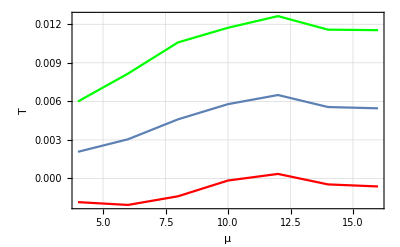

0.2

-Graphics-

0.3

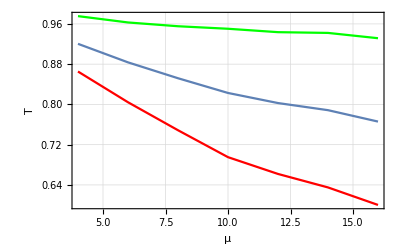

0.4

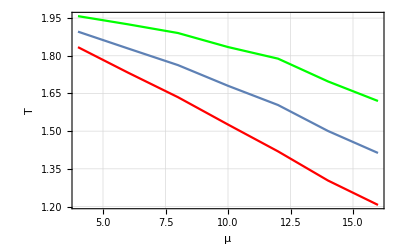

0.5

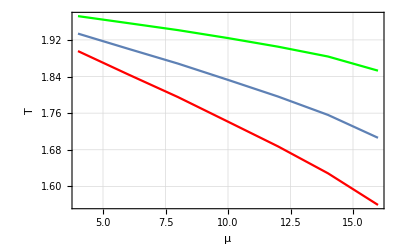

0.6

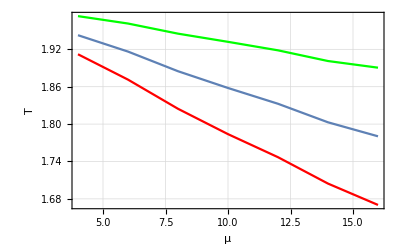

0.7

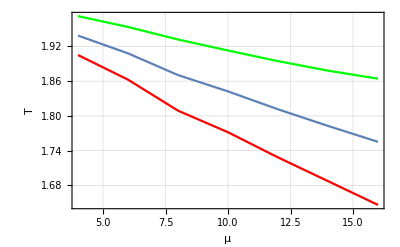

0.8

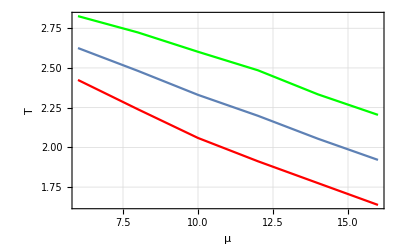

0.9

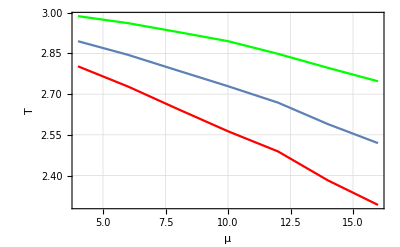

1.

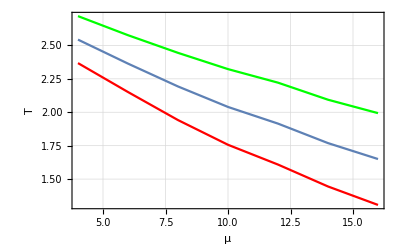

1.1

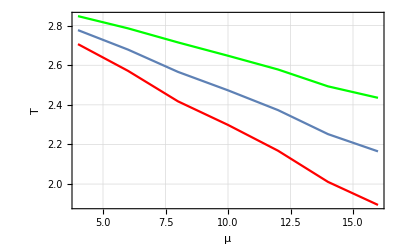

1.2

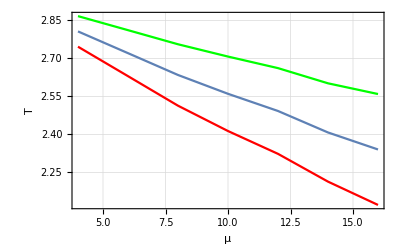

1.3

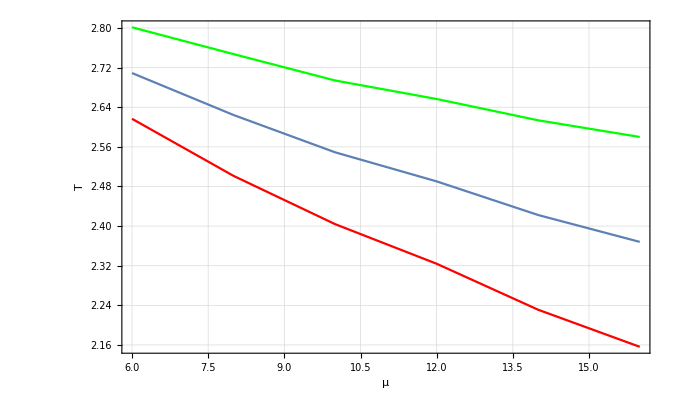

1.4

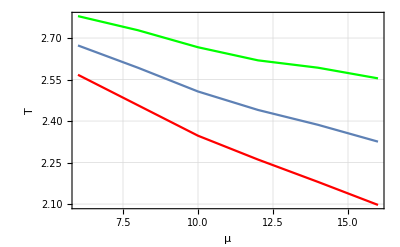

1.5

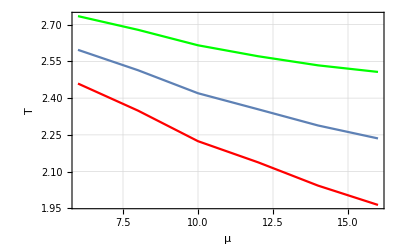

1.6

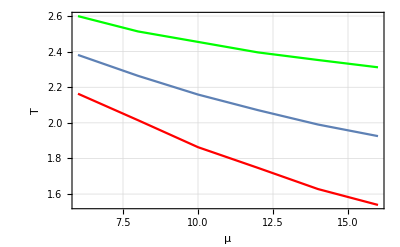

1.7

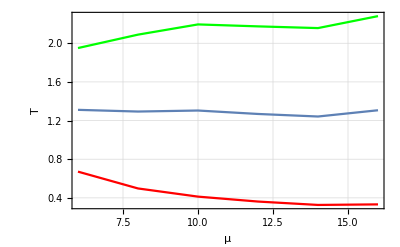

1.8

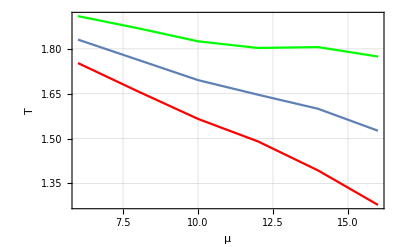

1.9

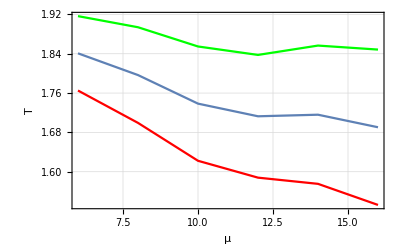

2.

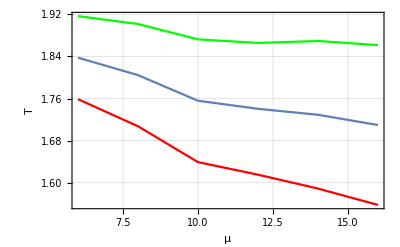

2.1

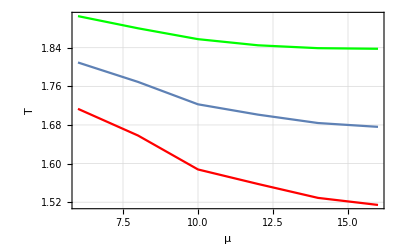

2.2

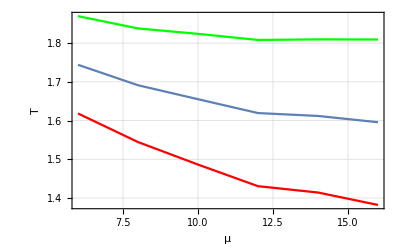

2.3

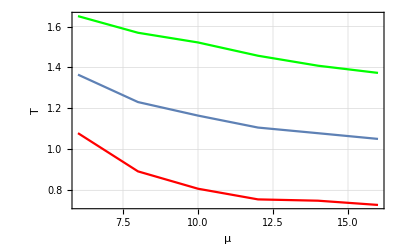

2.4

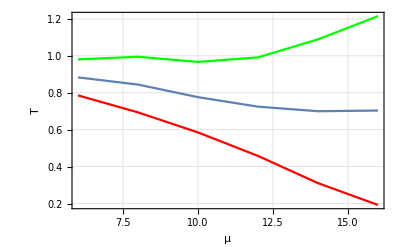

2.5

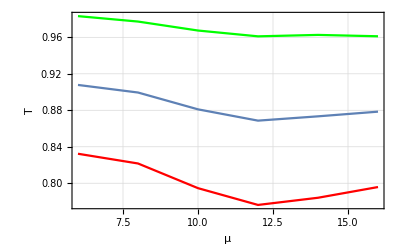

2.6

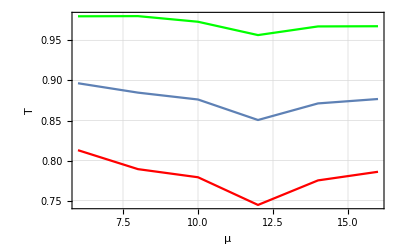

2.7

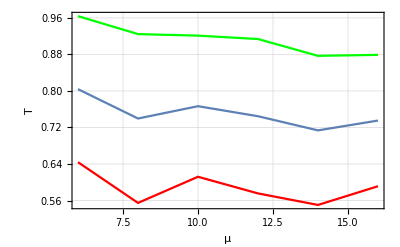

2.8

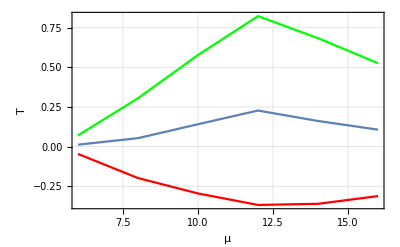

2.9

```mathematica
For[i=0.2,i<3,i+= 0.1,Print[λ[i,0.5]];Print[i]]
```

```mathematica
Manipulate[Show[λ[ω,0.5],{ω,Range[0.2,3,0.1]}]
```

```mathematica
Export["points.avi",%1134]
```

points.avi

```mathematica
SystemOpen["points.avi"]
```

```mathematica
λ[1.4,0.5]
```

-Graphics-